# Analyzing the Potential

```mathematica
Clear["Global`*"]
```

```mathematica
(*Takayama's Master Thesis*)
(*μ=2.7*10^-3;M=1.6;m = 2; g = 1; v= 6.4*10^-4; n= 10; CN = 0.1; Subscript[σ, i]=0.8;*)
(*Paper FIG1(a)*)
(*μ=2.04*10^-3; M=3; m=2; g=2*10^-5; v=4.7*10^-4; n = 4; CN = 0.04; Subscript[σ, i] = 0.4;*)
(*Paper FIG(a) lower potential fit to Planck data *)
μ=(2.04*10^-3)/3; M=0.17; m=2; g=2*10^-5; v=(4.7*10^-4)/3; n = 4; CN = 0.04; Subscript[σ, i] = 0.1;
(*Planck data exact*)
(*μ=7.06*10^-4; M=0.17; m=2; g=6.0*10^-4; v=1.57*10^-4; n = 4; CN = 0.04; Subscript[σ, i] = 0.11;*)

(*μ=2.0*10^-3;M=0.59; m = 2; g = 2.0*10^-5; v= 5.0*10^-4; n= 4; CN = 0.05; Subscript[σ, i] = 0.2;*)
Subscript[σ, c]= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(μ*M^(m-1))^(1/(2m-1)) ;(* The value of σ at the end of hybrid inflation *)
Subscript[σ, d]=  ((2m)/(2m-1))^((m-1)/(6m-4))*(4^(2m-1)/(2m*(2m-1))^m)^(1/(6m-4))*(μ*M^(m-1))^(1/(3m-2));
 Subscript[ϕ, init] = -v^2/μ^2*Subscript[σ, c]; (* The value of ϕ at the end of hybrid inflation *)

Subscript[ϕ, oscend] = -v^3/μ^3*Subscript[σ, c]; (* The value of ϕ at the end of oscillation period after hybrid inflation *)
Subscript[ϕ, oscendprecise] = Subscript[ϕ, oscend]*(Cos[Sqrt[5/3]*Log[μ/v]]+Sqrt[3/5]*Sin[Sqrt[5/3]*Log[μ/v]]);
(Cos[Sqrt[5/3]*Log[μ/v]]+Sqrt[3/5]*Sin[Sqrt[5/3]*Log[μ/v]])
Subscript[ψ, start]=  (4^m/((2m-1)*(2m)))^(1/(2m-2))*M*(μ/Subscript[σ, i])^(1/(m-1));
Subscript[ψ, end] = 2(μ*M^(m-1))^(1/m);

Subscript[ϕ, end] =  -√2*(v^2/g)^(1/n) ;(* The value of ϕ at the end of oscillation period after new inflation *)

VH[m_,M_,μ_, σ_,ψ_]:= ( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M^(2m-2)))*(-μ^2+ ψ^(2m)/(4^m * M^(2m-2)) ) ;
(*VH[m_,M_,μ_, σ_,ψ_]:= ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) *)

VN[v_,ϕ_,g_, CN_, n_]:= (v^2  - g/2^(n/2)ϕ^n)^2-CN/2*v^4*ϕ^2;

VI[m_,M_,μ_, σ_,ψ_,ϕ_,v_] := ( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * ϕ^2/2 -( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)))*v^2*σ*ϕ;

VH[m,M,μ, 0,Subscript[ψ, end]]
VN[v,ϕ,g, CN, n];
VI[m,M,μ, σ,ψ,ϕ,v];
Nefold = Integrate[VH[m,M,μ, σ,Subscript[ψ, start]]/D[VH[m,M,μ, σ,Subscript[ψ, start]],σ],{σ,Subscript[σ, c],Subscript[σ, i]}];
Nefoldappr =  Integrate[2/σ^3,{σ,Subscript[σ, d],Subscript[σ, i]}]+ Integrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(μ^(2/(m-1))*M^2)),{σ,Subscript[σ, c],Subscript[σ, d]}];
Nefoldappr2 =((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(μ*M^(m-1))^(-2/(3m-2));
Print["σ_c=",Subscript[σ, c]]
Print["σ_d=",Subscript[σ, d]]
Print["ψ_start=",Subscript[ψ, start]]
Print["ψ_end=",Subscript[ψ, end]]
Print["ϕ_init=",Subscript[ϕ, init]]
Print["ϕ_oscend=",Subscript[ϕ, oscend]]
Print["ϕ_oscendprecise=",Subscript[ϕ, oscendprecise]]
Print["ϕ_end=",Subscript[ϕ, end]]
Print["Nefold=",Nefold]
Print["Nefoldappr=",Nefoldappr]
Print["Nefoldappr2 =",Nefoldappr2 ]
{min,max}={10^-14,2*10^-11};

Show[
Plot3D[
VH[m,M,μ, σ,ψ](*+ VN[v,ϕ,g,CN,n] + VI[m,M,μ, σ,ψ,ϕ,v]*),{ψ,0,0.03},{σ,-0.2,1.4},ScalingFunctions->{"Reverse",None},PlotRange->{min,max}, AxesStyle->Directive[Black,FontSize->10],ColorFunction->(ColorData["SolarColors"][#3]&),ColorFunctionScaling->True,PlotLegends->BarLegend[{"SolarColors",{min,max}},LabelStyle->{Black}],Mesh -> 40, MeshStyle->Directive[Gray, Opacity[0.5]]
],

Graphics3D[Text[Style["ψ",16],Scaled[{0,-.15,0}]]],
Graphics3D[Text[Style["σ",16],Scaled[{1.1,1.1,0}]]],
Graphics3D[Text[Style["V",20],Scaled[{0,0,1.2}]]]
]
```

0.415517

0.

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

σ_c=0.0520118

σ_d=0.0971257

ψ_start=0.00133483

ψ_end=0.0215035

ϕ_init=-0.00276082

ϕ_oscend=-0.00063607

ϕ_oscendprecise=-0.000264298

ϕ_end=-0.264695

Nefold=100.945

Nefoldappr=40.5085

Nefoldappr2 =141.342

-Graphics3D-

# Zero mode EOM (by t)

```mathematica
Vbare[σ_,ψ_,ϕ_]:=VH[m,M,μ, σ,ψ]+VN[v,ϕ,g, CN, n]+VI[m,M,μ, σ,ψ,ϕ,v];
CNT = - Vbare[0,Subscript[ψ, end],Subscript[ϕ, end]];
V[ σ_,ψ_,ϕ_]:=Vbare[ σ,ψ,ϕ]+CNT;
Subscript[Γ, σ]=1*10^-11;Subscript[Γ, ψ]=1*10^-11;Subscript[Γ, ϕ]=1*10^-11;
ρ[ σ_,ψ_,ϕ_,rad_,t_] :=(D[σ,t]^2+D[ψ,t]^2+D[ϕ,t]^2)/2 + V[σ,ψ,ϕ]+rad;
p[ σ_,ψ_,ϕ_,rad_,t_] := (D[σ,t]^2+D[ψ,t]^2+D[ϕ,t]^2)/2 - V[σ,ψ,ϕ]+rad/3;
H[ σ_,ψ_,ϕ_,rad_,t_]:=Sqrt[ρ[ σ,ψ,ϕ,rad,t]/3];
Subscript[T, end]=10^9;
solution=NDSolve[
{
a''[t] == -(ρ[σ[t],ψ[t],ϕ[t],rad[t],t]+3p[σ[t],ψ[t],ϕ[t],rad[t],t])*a[t]/6,
(*a'[t]/a[t] == H[ σ[t],ψ[t],ϕ[t],rad[t],t],*)
D[(a[t]^4*rad[t]),t]/a[t]^4 == Subscript[Γ, σ]*σ'[t]^2+Subscript[Γ, ψ]*ψ'[t]^2+Subscript[Γ, ϕ]*ϕ'[t]^2,
σ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, σ])*σ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],σ[t]] == 0,
ψ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, ψ])*ψ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],ψ[t]] == 0,
ϕ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, ϕ])*ϕ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],ϕ[t]] == 0,
Nefolds'[t] == H[σ[t],ψ[t],ϕ[t],rad[t],t],
σ[0]==Subscript[σ, i],ψ[0]==Subscript[ψ, start],ϕ[0]==Subscript[ϕ, init],σ'[0]==0,ψ'[0]==0,ϕ'[0]==0,rad[0]==0,a[0]==1,a'[0]==H[σ[0],ψ[0],ϕ[0],0,rad[0]],Nefolds[0]== Log[a[0]]-135.6},{a,σ,ψ,ϕ,rad,Nefolds},{t,0,Subscript[T, end]},MaxSteps->Infinity]
```

{{a→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>],σ→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>],ψ→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>],ϕ→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>],rad→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>],Nefolds→                                 9
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

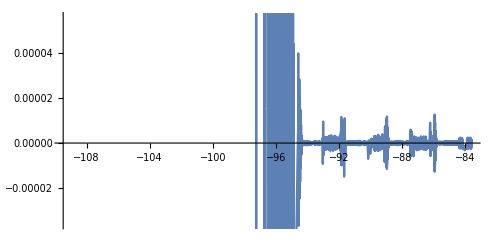

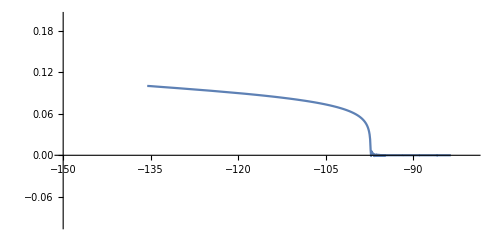

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],σ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500]
ParametricPlot[Evaluate[{Nefolds[t],σ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-150,-80},{-0.1,0.2}}]
```

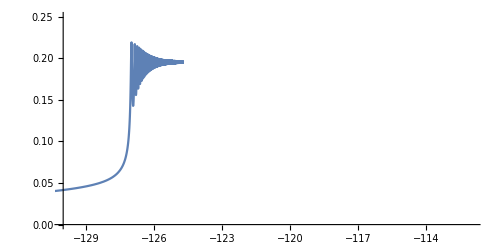

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],ψ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-130,-112},{0,0.25}}]
```

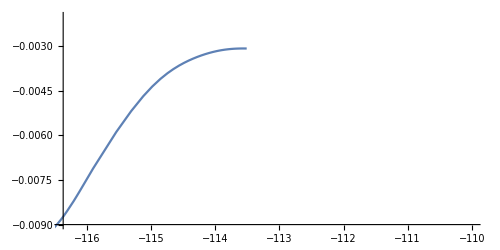

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],ϕ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-110},{-0.009,-0.002}}]
```

# Zero mode EOM (by N)

```mathematica
Vbare[σ_,ψ_,ϕ_]:=VH[m,M,μ, σ,ψ]+VN[v,ϕ,g, CN, n]+VI[m,M,μ, σ,ψ,ϕ,v];
CNT = - Vbare[0,Subscript[ψ, end],Subscript[ϕ, end]];
V[ σ_,ψ_,ϕ_]:=Vbare[ σ,ψ,ϕ]+CNT;
Subscript[Γ, σ]=1*10^-11;Subscript[Γ, ψ]=1*10^-11;Subscript[Γ, ϕ]=0;(*1*10^-11;*)
ρ[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_] :=(vsigma^2+vpsi^2+vphi^2)/2 + V[σ,ψ,ϕ]+rad;
p[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_] := (vsigma^2+vpsi^2+vphi^2)/2 - V[σ,ψ,ϕ]+rad/3;
H[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_]:=Sqrt[ρ[ σ,ψ,ϕ,vsigma,vpsi,vphi,rad]/3];
Subscript[Nefolds, init]= -135.6;
Subscript[Nefolds, end]=-110;

solution=NDSolve[
{

rad'[Nefolds]== -4 rad[Nefolds]+(Subscript[Γ, σ]*vsigma[Nefolds]^2+Subscript[Γ, ψ]*vpsi[Nefolds]^2+Subscript[Γ, ϕ]*vphi[Nefolds]^2)/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vsigma'[Nefolds]==-3vsigma[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],σ[Nefolds]]+Subscript[Γ, σ]*vsigma[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vpsi'[Nefolds]==-3vpsi[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],ψ[Nefolds]]+Subscript[Γ, ψ]*vpsi[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vphi'[Nefolds]==-3vphi[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],ϕ[Nefolds]]+Subscript[Γ, ϕ]*vphi[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

σ'[Nefolds] ==vsigma[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

ψ'[Nefolds]==vpsi[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]] ,

 ϕ'[Nefolds]==vphi[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

σ[Subscript[Nefolds, init]]==Subscript[σ, i],ψ[Subscript[Nefolds, init]]==Subscript[ψ, start],ϕ[Subscript[Nefolds, init]]==Subscript[ϕ, init],vsigma[Subscript[Nefolds, init]]==0,vpsi[Subscript[Nefolds, init]]==0,vphi[Subscript[Nefolds, init]]==0,rad[Subscript[Nefolds, init]]==0},{σ,ψ,ϕ,vsigma,vpsi,vphi,rad},{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},MaxSteps->Infinity,Method->Automatic]
```

{{σ→InterpolatingFunction[…],ψ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],vsigma→InterpolatingFunction[…],vpsi→InterpolatingFunction[…],vphi→InterpolatingFunction[…],rad→InterpolatingFunction[…]}}

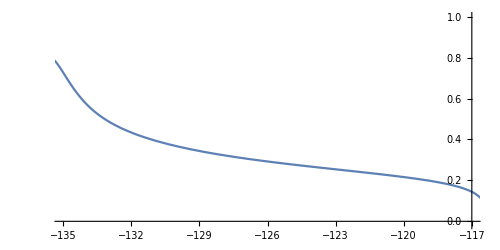

```mathematica
Plot[Evaluate[σ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-135.,-117},{-0.016,1}}]
```

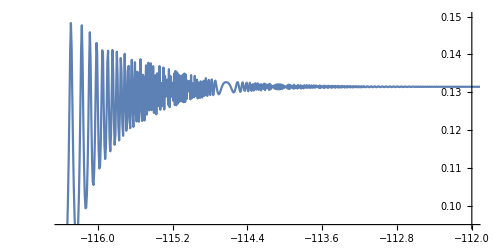

```mathematica
Plot[Evaluate[ψ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-112},{0.095,0.15}}]
```

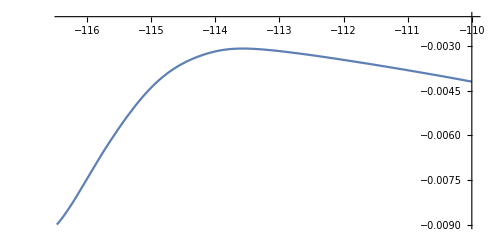

```mathematica
Plot[Evaluate[ϕ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-110},{-0.009,-0.002}}]
```

```mathematica
mσ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{σ[Nefolds],2}];
mψ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{ψ[Nefolds],2}];
mϕ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{ϕ[Nefolds],2}];
H2 = H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]]^2;
```

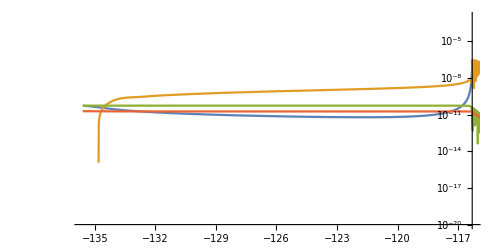

```mathematica
LogPlot[{Evaluate[mσ2/. solution],Evaluate[mψ2/. solution],Evaluate[mϕ2/. solution],Evaluate[H2 /. solution]},{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-135.6,-116.3},{10^(-20),10^(-3)}}]
```

# Important Parameters

## Effective Masses

```mathematica
Subscript[m, σ] = √((8 μ^3)/M)
Subscript[m, ψ] = √((8 μ^3)/M+16 μ^4)
```

0.000313712

0.000315064

## Field Values

```mathematica
Subscript[ϕ, init] = -v^3/μ^3*Subscript[σ, c]
Subscript[ϕ, 0] = -v^2/μ^2*Subscript[σ, c]
Subscript[ϕ, min] = N[-√2*(v^2/g)^(1/n)]
Subscript[ψ, end] = 2(μ*M^(m-1))^(1/m)
VH[m,M,μ, 0,Subscript[ψ, end]]+
VN[v,Subscript[ϕ, min],g, CN, n]+
VI[m,M,μ, 0,Subscript[ψ, end],Subscript[ϕ, min],v]
```

-0.00231593

-0.00977034

-0.324901

0.131453

-8.85507×10^-16

```mathematica
√(D[VH[m,M,μ, σ,Subscript[ψ, end]],{σ,2}]/. σ -> 0)
```

0.000313712

```mathematica
Subscript[a, osc] = -114.5;
Subscript[k, peak] = Exp[Subscript[a, osc]]*0.3*Subscript[m, σ]
```

1.76577×10^-54

## Perturbation EOM

```mathematica
F[Φ_] :=Sqrt[(1-2Φ)*(1+2Φ)^3] 
G[Φ_] :=D[F[Φ],Φ]
H[Φ_] :=D[F[Φ],Φ,Φ]
```

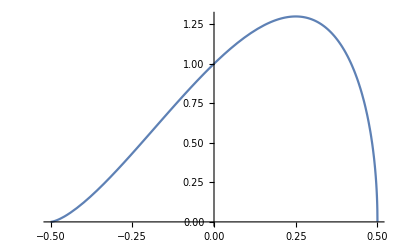

```mathematica
Plot[F[Φ],{Φ,-1/2,1/2}]
```

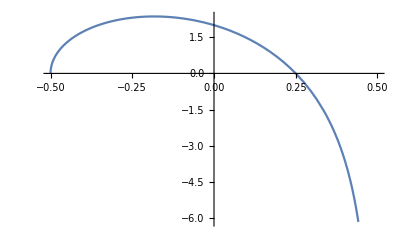

```mathematica
Plot[Evaluate@G[Φ],{Φ,-1/2,1/2}]
```

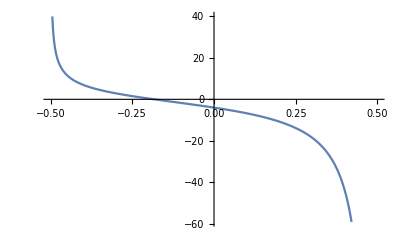

```mathematica
Plot[Evaluate@H[Φ],{Φ,-1/2,1/2}]
```

```mathematica
F[Φ]
G[Φ]
H[Φ]
Together[G[Φ]]
Together[H[Φ]]
```

√((1-2 Φ) (1+2 Φ)^3)

(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)/(2 √((1-2 Φ) (1+2 Φ)^3))

(24 (1-2 Φ) (1+2 Φ)-24 (1+2 Φ)^2)/(2 √((1-2 Φ) (1+2 Φ)^3))-((6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)^2)/(4 ((1-2 Φ) (1+2 Φ)^3)^(3/2))

-(2 (-1+12 Φ^2+16 Φ^3))/(√(-((-1+2 Φ) (1+2 Φ)^3)))

-(4 (1+2 Φ) (-1-4 Φ+8 Φ^2))/((-1+2 Φ) √(-((-1+2 Φ) (1+2 Φ)^3)))

```mathematica
F[Φ]/G[Φ]
H[Φ]/G[Φ]
Together[F[Φ]/G[Φ]]
Together[H[Φ]/G[Φ]]
```

(2 (1-2 Φ) (1+2 Φ)^3)/(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)

(2 √((1-2 Φ) (1+2 Φ)^3) ((24 (1-2 Φ) (1+2 Φ)-24 (1+2 Φ)^2)/(2 √((1-2 Φ) (1+2 Φ)^3))-((6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)^2)/(4 ((1-2 Φ) (1+2 Φ)^3)^(3/2))))/(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)

((-1+2 Φ) (1+2 Φ))/(2 (-1+4 Φ))

(2 (-1-4 Φ+8 Φ^2))/((-1+2 Φ) (1+2 Φ) (-1+4 Φ))

## σ_c behavior

```mathematica
Subscript[σ, c][m_,μ_,M_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(μ*M^(m-1))^(1/(2m-1))
```

```mathematica
μ=2.7*10^-3;M=1.6; 
Plot3D[Subscript[σ, c][m,μ,M],{m,2,10},{μ,10^-3,10^-2}]
```

-Graphics3D-

## Calculating potential variables from observation variables

### Previous Research (WMAP)

```mathematica
R = 4.7*10^-5; (*amplitude of curvature perturbation*)

(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24(3m-1)*(m-1)*nsrun))^(1/4)
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))
(*mu*)
mu[ns_ , nsrun_, m_ ]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))
(*M*)
M[ns_ , nsrun_, m_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m ] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m ]*(M[ns , nsrun, m])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m]*(mu[ns , nsrun, m ]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_] := 2(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(1/m);

VH[ns_ , nsrun_, m_, σ_,ψ_]:= ( -mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m*M[ns , nsrun, m]^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M[ns , nsrun, m])^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m]^(2m-2)))*(-mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m * M[ns , nsrun, m]^(2m-2)) ) 

Nr1[ns_ , nsrun_, m_] := NIntegrate[VH[ns , nsrun, m, σ, psistart[ns , nsrun, m]]/D[VH[ns, nsrun, m, σ, psistart[ns , nsrun, m]],σ],{σ,sigmac[ns , nsrun, m ],sigma[ns , nsrun, m ]}];
Nr2[ns_ , nsrun_, m_] :=  NIntegrate[2/σ^3,{σ,sigmad[ns , nsrun, m],sigma[ns , nsrun, m ]}]+ NIntegrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(mu[ns , nsrun, m ]^(2/(m-1))*M[ns , nsrun, m]^2)),{σ,sigmac[ns , nsrun, m ],sigmad[ns , nsrun, m]}];
Nr3[ns_ , nsrun_, m_] :=((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(-2/(3m-2));
```

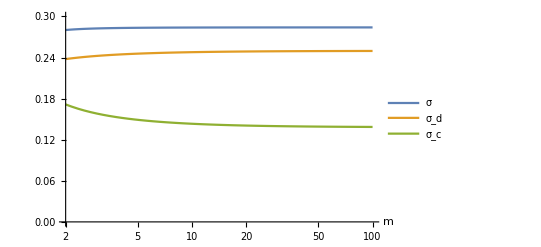

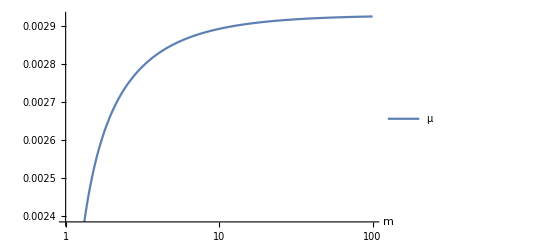

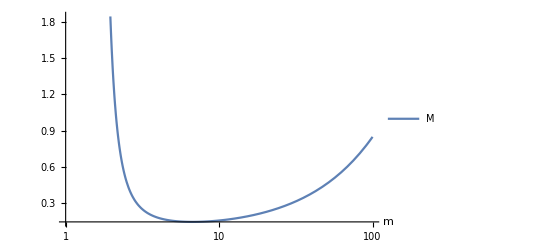

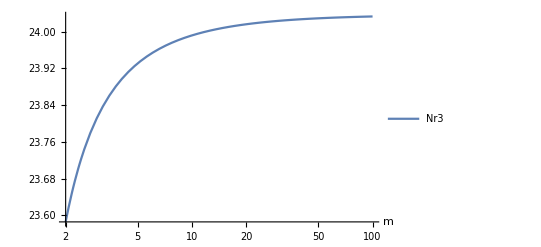

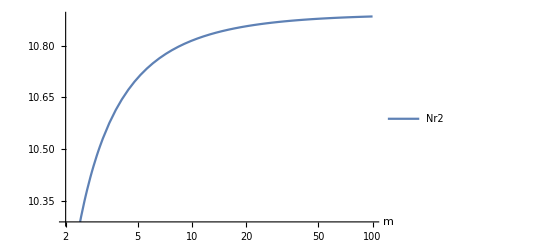

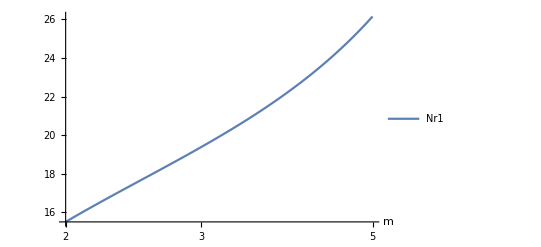

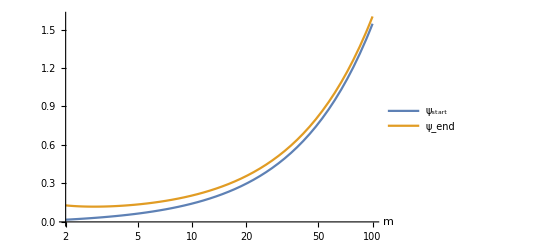

```mathematica
ns = 1.13; nsrun = -0.055;
LogLinearPlot[{sigma[ns, nsrun, m ],sigmad[ns, nsrun, m ],sigmac[ns, nsrun, m ]} ,{m,2,100},PlotRange->{0,0.3},AxesLabel->{"m"},PlotLegends->{"σ","σ_d","σ_c"}]
LogLinearPlot[mu[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{μ}]
LogLinearPlot[M[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{M}]
LogLinearPlot[Nr3[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr3}]
LogLinearPlot[Nr2[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr2}]
LogLinearPlot[Nr1[ns, nsrun, m ] ,{m,2,5},AxesLabel->{"m"},PlotLegends->{Nr1}]
(*LogLinearPlot[{Nr1[ns, nsrun, m ],Nr2[ns, nsrun, m ],Nr3[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr1,Nr2,Nr3}]*)
LogLinearPlot[{psistart[ns, nsrun, m ],psiend[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{"ψ_start","ψ_end"}]
(*LogLinearPlot[psiend[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Subscript[ψ, end]}]*)
```

```mathematica
ns = 1.13; nsrun = -0.055;m =2;
```

```mathematica
Print["σ = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m]", μ = ",mu[ns , nsrun, m ]", M = ",M[ns , nsrun, m ]]
Print["ψ_start= ",psistart[ns , nsrun, m]", ψ_end = ",psiend[ns , nsrun, m]]
Print["Nr1 = ",Nr1[ns , nsrun, m ]", Nr2 = ",Nr2[ns , nsrun, m ]", Nr3 = ",Nr3[ns , nsrun, m ]]
```

σ = 0.280196 , σ_d = 0.237765 , σ_c = 0.171601 , μ = 0.00263784 , M = 1.57385

ψ_start= 0.0171088 , ψ_end = 0.128865

Nr1 = 15.5021 , Nr2 = 10.0148 , Nr3 = 23.5854

```mathematica
ClearAll["Global`*"]
```

### Planck Data

```mathematica
R = Sqrt[Exp[3.044]*10^-10] (*amplitude of curvature perturbation*)

(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12*(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24*(3m-1)*(m-1)*nsrun))^(1/4);
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2));
(*mu*)
mu[ns_ , nsrun_, m_ ]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3));
(*M*)
M[ns_ , nsrun_, m_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m ] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1));
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m ]*(M[ns , nsrun, m])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m]*(mu[ns , nsrun, m ]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_] := 2(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(1/m);

VH[ns_ , nsrun_, m_, σ_,ψ_]:= ( -mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m*M[ns , nsrun, m]^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M[ns , nsrun, m])^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m]^(2m-2)))*(-mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m * M[ns , nsrun, m]^(2m-2)) ) 

Nr1[ns_ , nsrun_, m_]:= NIntegrate[VH[ns , nsrun, m, σ, psistart[ns , nsrun, m]]/D[VH[ns, nsrun, m, σ, psistart[ns , nsrun, m]],σ],{σ,sigmac[ns , nsrun, m ],sigma[ns , nsrun, m ]}];
Nr2[ns_ , nsrun_, m_] :=  Integrate[2/σ^3,{σ,sigmad[ns , nsrun, m],sigma[ns , nsrun, m ]}]+ Integrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(mu[ns , nsrun, m ]^(2/(m-1))*M[ns , nsrun, m]^2)),{σ,sigmac[ns , nsrun, m ],sigmad[ns , nsrun, m]}];
Nr3[ns_ , nsrun_, m_] :=((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(-2/(3m-2));
```

0.0000458138

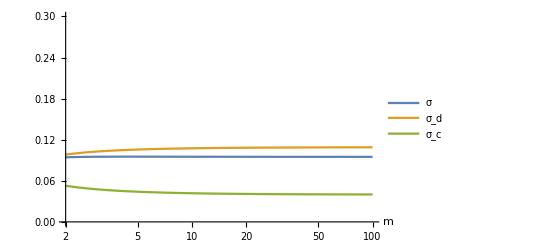

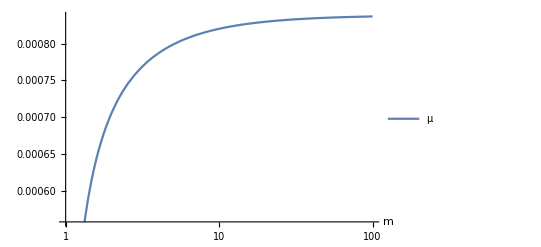

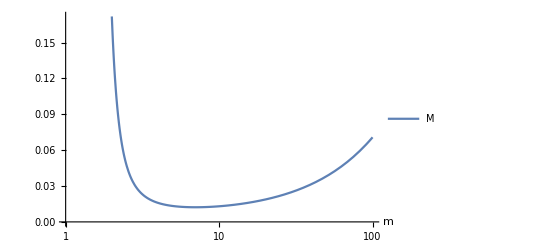

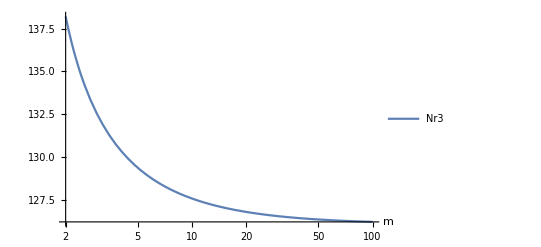

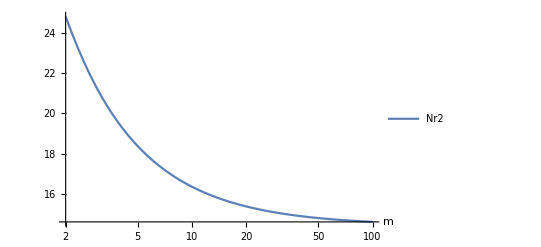

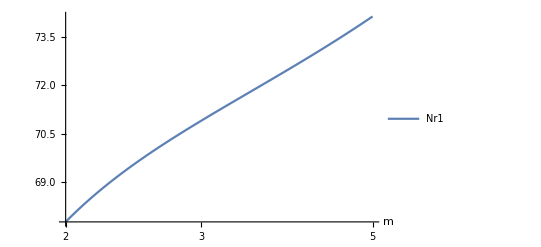

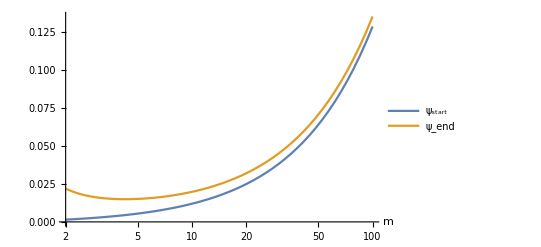

```mathematica
ns = 0.9649; nsrun = -0.0045;
LogLinearPlot[{sigma[ns, nsrun, m ],sigmad[ns, nsrun, m ],sigmac[ns, nsrun, m ]} ,{m,2,100},PlotRange->{0,0.3},AxesLabel->{"m"},PlotLegends->{"σ","σ_d","σ_c"}]
LogLinearPlot[mu[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{μ}]
LogLinearPlot[M[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{M}]
LogLinearPlot[Nr3[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr3}]
LogLinearPlot[Nr2[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr2}]
LogLinearPlot[Nr1[ns, nsrun, m ] ,{m,2,5},AxesLabel->{"m"},PlotLegends->{Nr1}]
(*LogLinearPlot[{Nr1[ns, nsrun, m ],Nr2[ns, nsrun, m ],Nr3[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr1,Nr2,Nr3}]*)
LogLinearPlot[{psistart[ns, nsrun, m ],psiend[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{"ψ_start","ψ_end"}]
(*LogLinearPlot[psiend[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Subscript[ψ, end]}]*)
```

```mathematica
m = 2;
Print["σ = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m]", μ = ",mu[ns , nsrun, m ]", M = ",M[ns , nsrun, m ]]
Print["ψ_start= ",psistart[ns , nsrun, m]", ψ_end = ",psiend[ns , nsrun, m]]
Print["Nr1 = ",Nr1[ns , nsrun, m ]", Nr2 = ",Nr2[ns , nsrun, m ]", Nr3 = ",Nr3[ns , nsrun, m ]]
```

σ = 0.0942573 , σ_d = 0.0982195 , σ_c = 0.0527943 , μ = 0.000706379 , M = 0.171149

ψ_start= 0.00148104 , ψ_end = 0.0219905

Nr1 = 67.7477 , Nr2 = 24.8217 , Nr3 = 138.211

## Range of parameters in the case of Planck data

### Use data of TT,TE,EE+lowE+lensing (eq (13) and eq (15))

```mathematica
(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12*(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24*(3m-1)*(m-1)*nsrun))^(1/4)/; nsrun ≥ ((m+1)^2(ns-1)^2)/(24*(3m-1)*(m-1))

(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))

(*mu*)
mu[ns_ , nsrun_, m_ ]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3));
(*M*)
M[ns_ , nsrun_, m_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m ] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1));
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m ]*(M[ns , nsrun, m])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m]*(mu[ns , nsrun, m ]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_] := 2(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(1/m);

VH[ns_ , nsrun_, m_, σ_,ψ_]:= ( -mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m*M[ns , nsrun, m]^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M[ns , nsrun, m])^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m]^(2m-2)))*(-mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m * M[ns , nsrun, m]^(2m-2)) ) 

Nr1[ns_ , nsrun_, m_]:= NIntegrate[VH[ns , nsrun, m, σ, psistart[ns , nsrun, m]]/D[VH[ns, nsrun, m, σ, psistart[ns , nsrun, m]],σ],{σ,sigmac[ns , nsrun, m ],sigma[ns , nsrun, m ]}];
Nr2[ns_ , nsrun_, m_] :=  Integrate[2/σ^3,{σ,sigmad[ns , nsrun, m],sigma[ns , nsrun, m ]}]+ Integrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(mu[ns , nsrun, m ]^(2/(m-1))*M[ns , nsrun, m]^2)),{σ,sigmac[ns , nsrun, m ],sigmad[ns , nsrun, m]}];
Nr3[ns_ , nsrun_, m_] :=((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(-2/(3m-2));
```

```mathematica
nsmean = 0.9649; nsonesigma = 0.0042;
nsmin = nsmean -nsonesigma; nsmax =nsmean +nsonesigma;
Print["Data of TT,TE,EE+lowE+lensing \n ns:"]
Print["mean = ", nsmean,"  min = ", nsmin,"  max = ", nsmax]

nsrunmean = −0.0045; nsrunonesigma = 0.0067;
nsrunmin = nsrunmean -nsrunonesigma; nsrunmax =nsrunmean +nsrunonesigma;
Print["\n Data of TT,TE,EE+lowE+lensing \n ns_run:"]
Print["mean = ", nsrunmean,"  min = ", nsrunmin,"  max = ", nsrunmax]

mvar = 2;

(*Value inside of square root must be greater than zero
(m+1)^2(ns-1)^2≥24*(3m-1)*(m-1)*nsrun
*)
nsrunmaxconstraintmax = ((mvar+1)^2(nsmax-1)^2)/(24*(3mvar-1)*(mvar-1))
nsrunmaxconstraintmin= ((mvar+1)^2(nsmin-1)^2)/(24*(3mvar-1)*(mvar-1))
(*Print["nsrunmaxconstraint:", nsrunmaxconstraint]

nsrunmaxfinal =If[nsrunmaxconstraint<nsrunmax,nsrunmaxconstraint,nsrunmax];
Print["nsrunmaxfinal:", nsrunmaxfinal]*)

Plot3D[sigma[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]

FindMaximum[{sigma[nsvar,nsrunvar, mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{sigma[nsvar,nsrunvar,mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmin≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Plot3D[sigmad[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]

FindMaximum[{sigmad[nsvar,nsrunvar, mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{sigmad[nsvar,nsrunvar,mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmin≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Plot3D[mu[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
Plot3D[M[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
```

Data of TT,TE,EE+lowE+lensing 
 ns:

mean = 0.9649  min = 0.9607  max = 0.9691

Data of TT,TE,EE+lowE+lensing 
 ns_run:

mean = -0.0045  min = -0.0112  max = 0.0022

0.0000716108

0.000115837

-Graphics3D-

{0.135778,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::nrnum: 関数の値6.22937×10^-6+6.22937×10^-6 ⅈは{nsvar,nsrunvar} = {0.967865,-0.000619589}において実数ではありません．

FindMinimum::nrnum: 関数の値8.19832×10^-6+8.19832×10^-6 ⅈは{nsvar,nsrunvar} = {0.967865,-0.000619589}において実数ではありません．

General::stop: この計算中に，FindMinimum::nrnumのこれ以上の出力は表示されません．

FindMinimum::eit: アルゴリズムは500回の反復では許容範囲1.×10^-6に収束しませんでした．求められた最適な残差である，{6.00856×10^-22,66.0945,2.32758×10^-22}の{実行可能残差, KKT残差, 付加残差}が返されます．

{0.00131747,{nsvar→0.968174,nsrunvar→-0.000608146}}

-Graphics3D-

{0.134646,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.000112244,{nsvar→0.966315,nsrunvar→-0.00068082}}

-Graphics3D-

-Graphics3D-

```mathematica
(*amplitude of curvature perturbation*)

Rexpmean = 3.044; Rexponesigma = 0.014;
Rexpmin = Rexpmean - Rexponesigma; Rexpmax = Rexpmean + Rexponesigma;
Print["Data of TT,TE,EE+lowE+lensing \n ln(10^10A_s):"]
(*Print["Data of TT,TE,EE+lowE+lensing \n ln10^10A_s:"];*)
Print["mean = ", Rexpmean,"  min = ", Rexpmin,"  max = ", Rexpmax];
Rmean = Sqrt[Exp[Rexpmean]*10^-10];
Rmin =  Sqrt[Exp[Rexpmin]*10^-10];
Rmax =  Sqrt[Exp[Rexpmax]*10^-10];
Print["Data of TT,TE,EE+lowE+lensing \n A_s:"]
Print["mean = ", ScientificForm[Rmean],"  min = ", ScientificForm[Rmin], "  max = ", ScientificForm[Rmax]]


(*mu*)
mu[ns_ , nsrun_, m_ ,R_]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))

Rvar = Rmean;
Print["R: mean = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Rvar = Rmin;
Print["R: min = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Rvar = Rmax;
Print["R: max = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]
```

Data of TT,TE,EE+lowE+lensing 
 ln(10^10A_s):

mean = 3.044  min = 3.03  max = 3.058

Data of TT,TE,EE+lowE+lensing 
 A_s:

mean = 4.58138×10^-5  min = 4.54942×10^-5  max = 4.61356×10^-5

R: mean = 4.58138×10^-5

-Graphics3D-

{0.00109864,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.,{nsvar→0.964885,nsrunvar→-0.000739821}}

R: min = 4.54942×10^-5

-Graphics3D-

{0.0010948,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.,{nsvar→0.964883,nsrunvar→-0.000739932}}

R: max = 4.61356×10^-5

-Graphics3D-

{0.00110249,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::sdir: Search direction has become too small.

{0.,{nsvar→0.964888,nsrunvar→-0.000739708}}

```mathematica
(*M*)
M[ns_ , nsrun_, m_ ,R_]:= ( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns, nsrun, m ,R] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
Rvar = Rmean;
Print["R: mean = ", ScientificForm[Rvar]]
Plot3D[M[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{M[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{M[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]
```

R: mean = 4.58138×10^-5

-Graphics3D-

{0.388537,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{4.80701×10^-7,{nsvar→0.964549,nsrunvar→-0.000754131}}

```mathematica
FEfold[m_]:=Integrate[1/(y^3+y^(-(3m-1)/(m-1))),{y,0,1}];
FEfold[2]
FEfold[3]
```

(π+Log[3-2 √2])/(8 √2)

1/49 (Log[128]-7 Cos[π/7] Log[2-2 Sin[π/14]]-7 Log[2 (1+Sin[(3 π)/14])] Sin[π/14]+π (-2 Cos[π/14]+6 Cos[(3 π)/14]+4 Sin[π/7])+7 Log[4 Sin[π/14]^2] Sin[(3 π)/14])

```mathematica
Integrate[Sin[x]^3,{x,0,Pi/2}]
Integrate[Sqrt[t]/(4*(t^2 + 1)),{t,0,1}]
```

2/3

(π+Log[3-2 √2])/(8 √2)

```mathematica
Rmaxsol = Solve[Log[10^10*Rmax^2] == 3.044 + 0.014 ,Rmax];
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rminsol = Solve[Log[10^10*Rmin^2] == 3.044 - 0.014 ,Rmin];
Rmax = ScientificForm[(Rmax/.Rmaxsol)[[1]]]
Rmean = ScientificForm[(Rmean/.Rmeansol)[[1]]]
Rmin = ScientificForm[(Rmin/.Rminsol)[[1]]]
Rplus = 4.61356 - 4.58138
Rminus = 4.54942 - 4.58138
```

4.61356×10^-5

4.58138×10^-5

4.54942×10^-5

0.03218

-0.03196

## Calculating potential variables from observation variables (FINAL)

### Previous Research (WMAP)

```mathematica
ClearAll["Global`*"]

(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24(3m-1)*(m-1)*nsrun))^(1/4)
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))
(*mu*)
mu[ns_ , nsrun_, m_ ,R_]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))
(*M*)
M[ns_ , nsrun_, m_,R_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m, R] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_, R_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m, R ]*(M[ns , nsrun, m, R])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_,R_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/sigma[ns , nsrun, m ])^(1/(m-1));
psistartprecise[ns_ , nsrun_, m_,R_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/sigma[ns , nsrun, m ])^(1/(m-1))*(((1+m*sigma[ns , nsrun, m ]^2)+√((m*sigma[ns , nsrun, m ]^2-1)^2+2*sigma[ns , nsrun, m ]^2))/2)^(1/(2m-2));
psiend[ns_ , nsrun_, m_, R_] := 2(mu[ns , nsrun, m , R]*M[ns , nsrun, m, R]^(m-1))^(1/m);

psiinfmin[ns_ , nsrun_, m_, R_,σ_] :=(4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/σ)^(1/(m-1));
psiinfminprecise[ns_ , nsrun_, m_, R_,σ_] := (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/σ)^(1/(m-1))*(((1+m*σ^2)+√((m*σ^2-1)^2+2*σ^2))/2)^(1/(2m-2));

VH[ns_ , nsrun_, m_, σ_, R_]:= ( -mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)) )^2 * (1+σ^4/8+(psiinfmin[ns , nsrun, m, R,σ])^2/2)+ ((m^2*σ^2*(psiinfmin[ns , nsrun, m, R,σ])^2)/4^(2m-1))*(psiinfmin[ns , nsrun, m, R,σ]/M[ns , nsrun, m, R])^(4m-4) + ((m * (psiinfmin[ns , nsrun, m, R,σ])^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2)) ); 
VHExact[ns_ , nsrun_, m_, σ_, R_]:=　Exp[ σ^2/2+(psiinfmin[ns , nsrun, m, R,σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfmin[ns , nsrun, m, R,σ])^(2m-1)/M[ns , nsrun, m, R]^(2(m-1))+psiinfmin[ns , nsrun, m, R,σ]/2*(-mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))))^2);
VHpsiprecise[ns_ , nsrun_, m_, σ_, R_]:= ( -mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)) )^2 * (1+σ^4/8+(psiinfminprecise[ns , nsrun, m, R,σ])^2/2)+ ((m^2*σ^2*(psiinfminprecise[ns , nsrun, m, R,σ])^2)/4^(2m-1))*(psiinfminprecise[ns , nsrun, m, R,σ]/M[ns , nsrun, m, R])^(4m-4) + ((m * (psiinfminprecise[ns , nsrun, m, R,σ])^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2)) ); 
VHExactpsiprecise[ns_ , nsrun_, m_, σ_, R_]:=　Exp[ σ^2/2+(psiinfminprecise[ns , nsrun, m, R,σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfminprecise[ns , nsrun, m, R,σ])^(2m-1)/M[ns , nsrun, m, R]^(2(m-1))+psiinfminprecise[ns , nsrun, m, R,σ]/2*(-mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))))^2);

VH01234[ns_ , nsrun_, m_, σ_, R_]:= mu[ns , nsrun, m , R]^4+ mu[ns , nsrun, m , R]^4*σ^4/8+mu[ns , nsrun, m , R]^4*psiinfminprecise[ns , nsrun, m, R, σ]^2/2-2*mu[ns , nsrun, m , R]^2* psiinfminprecise[ns , nsrun, m, R, σ]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*σ^2*psiinfminprecise[ns , nsrun, m, R, σ]^2)/4^(2m-1))*(psiinfminprecise[ns , nsrun, m, R, σ]/M[ns , nsrun, m, R])^(4m-4)+((m * psiinfminprecise[ns , nsrun, m, R, σ]^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 );
xiprecise[ns_ , nsrun_, m_, σ_, R_]:= (Derivative[0,0,0,3,0][VH01234][ns , nsrun, m, σ, R]* Derivative[0,0,0,1,0][VH01234][ns , nsrun, m, σ, R])/(mu[ns , nsrun, m , R]^4)^2


NrPotInt[ns_ , nsrun_, m_, R_] := NIntegrate[VH[ns , nsrun, m, σ, R]/D[VH[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotIntExact[ns_ , nsrun_, m_, R_] := NIntegrate[VHExact[ns , nsrun, m, σ, R]/D[VHExact[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotIntpsiprecise[ns_ , nsrun_, m_, R_] := NIntegrate[VHpsiprecise[ns , nsrun, m, σ, R]/D[VHpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotIntExactpsiprecise[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];

NrEst1[ns_ , nsrun_, m_, R_] := If[sigma[ns , nsrun, m ]> sigmad[ns , nsrun, m ],
								((3m-2)/(2m-1))*1/(sigmad[ns , nsrun, m ])^2-1/(sigma[ns , nsrun, m ])^2,
								((m-1)/(2m-1))*1/(sigmad[ns , nsrun, m ])^2*(sigma[ns , nsrun, m ]/sigmad[ns , nsrun, m ])^((4m-2)/(m-1))];
NrEst2[ns_ , nsrun_] := 1/(sigmad[ns , nsrun, 2 ])^2((Pi-Log[3+Sqrt[2]])/(4*Sqrt[2])-1+sigma[ns , nsrun, 2 ]/sigmad[ns , nsrun, 2 ]);

termsubtract[ns_ , nsrun_, m_ , R_]:=VHExact[ns , nsrun, m, sigma[ns , nsrun, m ], psistart[ns, nsrun, m ,R], R] - mu[ns , nsrun, m , R]^4;
term0[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*sigma[ns , nsrun, m ]^4/8;
term1[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistart[ns, nsrun, m ,R]^2/2;
term2[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4[ns_ , nsrun_, m_ , R_] := Abs[((m * psistart[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * psistart[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2)];

termsubtractprecise[ns_ , nsrun_, m_ , R_]:=VHExact[ns , nsrun, m, sigma[ns , nsrun, m ], psistartprecise[ns, nsrun, m ,R], R] - mu[ns , nsrun, m , R]^4;
term0precise[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*sigma[ns , nsrun, m ]^4/8;
term1precise[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R]^2/2;
term2precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3precise[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4precise[ns_ , nsrun_, m_ , R_] := Abs[((m * psistartprecise[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * psistartprecise[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2)];


term1div[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R];
term2div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3div[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4div[ns_ , nsrun_, m_ , R_] := Abs[((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term1234div[ns_ , nsrun_, m_ , R_] := Abs[mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R]-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
```

$Aborted

NIntegrate::ncvb: NIntegrateが{σ} = {0.049081}の近傍のσで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-0.863378と0.00610543を得ました．

NIntegrate::slwcon: 数値積分の収束が遅すぎます．特異性がある，積分の値がゼロ，被積分関数が激しく振動する，あるいはWorkingPrecisionが小さすぎるのいずれかが原因である可能性があります．

NIntegrate::ncvb: NIntegrateが{σ} = {0.0296304860279494}の近傍のσで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-0.87548と0.0231788を得ました．

NIntegrate::ncvb: NIntegrateが{σ} = {0.0230567995223055}の近傍のσで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-0.870452と0.00904479を得ました．

General::stop: この計算中に，NIntegrate::ncvbのこれ以上の出力は表示されません．

NIntegrate::slwcon: 数値積分の収束が遅すぎます．特異性がある，積分の値がゼロ，被積分関数が激しく振動する，あるいはWorkingPrecisionが小さすぎるのいずれかが原因である可能性があります．

General::stop: この計算中に，NIntegrate::slwconのこれ以上の出力は表示されません．

ListPlot::lpn: {{{2.,6.98996},{3.,7.86626},{4.,8.58787},{5.,9.33541},{6.,10.1679},{7.,«19»},{8.,12.2639},{9.,13.6387},{10.,15.3459},{11.,17.5323}},«5»,{{«1»},«9»}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

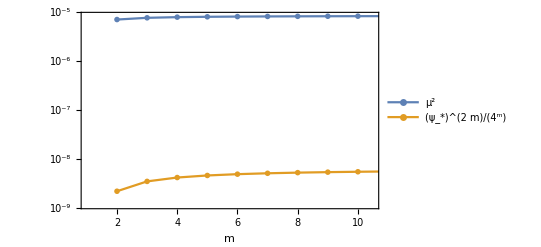
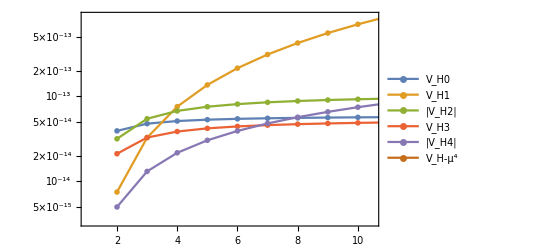
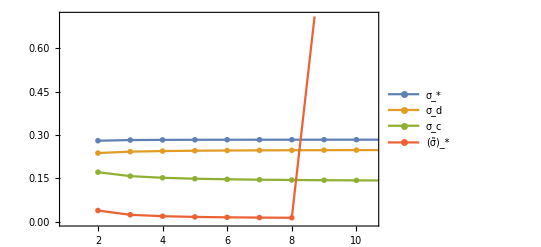
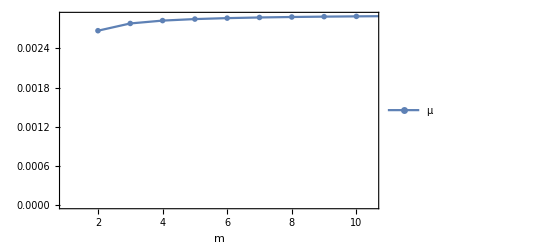
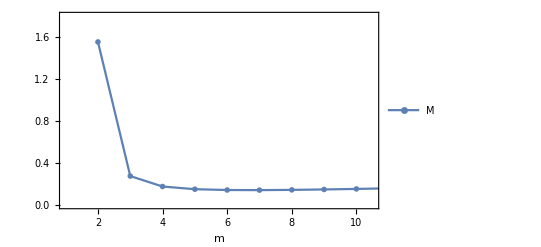
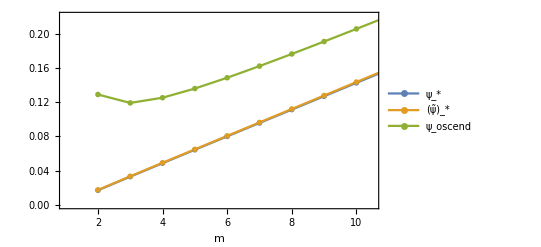
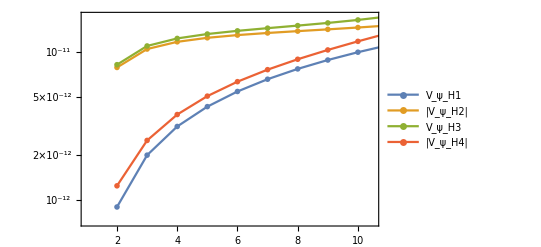
[◼] | PlotGrid[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,ListPlot[{{{2,6.98996},{3,7.86626},{4,8.58787},{5,9.33541},{6,10.1679},{7,11.1282},{8,12.2639},{9,13.6387},{10,15.3459},{11,17.5323}},{{2,6.8853},{3,7.69079},{4,8.31559},{5,8.91281},{6,9.51701},{7,10.1398},{8,10.7855},{9,11.4547},{10,12.1463},{11,12.8577}},{{2,10.8482},{3,11.2865},{4,11.421},{5,11.4836},{6,11.5192},{7,11.542},{8,11.5577},{9,11.5692},{10,11.578},{11,11.5849}},{{2,8.33751}},NrPotInttablepsiprecise,NrPotIntExacttablepsiprecise,{{2,-0.863378},{3,-0.87548},{4,-0.870452},{5,-0.876238},{6,-0.89685},{7,-0.917355},{8,-0.942865},{9,20.8252},{10,21.535},{11,22.253}}},Joined→True,PlotMarkers→-Graphics-,PlotRange→{{1,10.5},{0,Automatic}},Ticks→{{0,1,2,3,4,5},Automatic},PlotLegends→Placed[{N_HVaψa,N_HVpψa,N_Hest1,N_Hest2,N_HVaψp,N_HVpψp,N_HVpψpσp},{Left,Top}],LabelStyle→Directive[GrayLevel[0]],Frame→True,FrameLabel→{m},FrameStyle→Automatic,FrameTicks→All]}},FrameStyle→GrayLevel[0],ImageSize→{900,900}]

SHI_m.eps

```mathematica
ns = 1.13; nsrun = -0.055;
R = 4.7*10^-5; (*amplitude of curvature perturbation*)

mmax = 10;



mu2table = Table[{m,mu[ns , nsrun, m, R ]^2},{m,2,mmax+1}];
psi2mtable = Table[{m,psistart[ns, nsrun, m ,R]^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2))},{m,2,mmax+1}];
plot0 = ListLogPlot[{mu2table,psi2mtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},Automatic},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"μ^2","(ψ_*)^(2  m)/4^m"},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];



term0table = Table[{m,term0[ns , nsrun, m , R]},{m,2,mmax+1}];
term1table = Table[{m,term1[ns , nsrun, m , R]},{m,2,mmax+1}];
term2table = Table[{m,term2[ns , nsrun, m , R]},{m,2,mmax+1}];
term3table = Table[{m,term3[ns , nsrun, m , R]},{m,2,mmax+1}];
term23table = Table[{m,term23[ns , nsrun, m , R]},{m,2,mmax+1}];
term4table = Table[{m,term4[ns , nsrun, m , R]},{m,2,mmax+1}];
term234table = Table[{m,term234[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtracttable = Table[{m,termsubtract[ns , nsrun, m , R]},{m,2,mmax+1}];
(*term5table = Table[{m,term5[ns , nsrun, m , R]},{m,2,mmax+1}];
term6table = Table[{m,term6[ns , nsrun, m , R]},{m,2,mmax+1}];*)
plot1 = ListLogPlot[{term0table,term1table,term2table,term3table,term4table,termsubtracttable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{Automatic,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{Style["V_H0",10],Style["V_H1",10],Style["|V_H2|",10],Style["V_H3",10],Style["|V_H4|",10],Style["V_H-μ^4",10]},{Left,Top}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

sigmatable = Table[{m,sigma[ns, nsrun, m ]},{m,2,mmax+1}];
sigmadtable = Table[{m,sigmad[ns, nsrun, m ]},{m,2,mmax+1}];
sigmactable = Table[{m,sigmac[ns, nsrun, m ,R]},{m,2,mmax+1}];

(*Func[ns_, nsrun_, m_,σ_]:=
(-((2m-1)(2m-3)(m+1)m)/(2(m-1)^2(3m-1))(3 σ^2-ns+1)+(2m-1)/((m-1)σ)(3 σ^2-ns+1)+3σ)*(-((2m-1)(2m-3))/(2(3m-1))(3 σ^2-ns+1)σ^3+(m-1)/(3m-1)(3 σ^2-ns+1)σ+σ^3)+nsrun*)

Func[ns_, nsrun_, m_,σ_,R_]:= 2*xiprecise[ns, nsrun, m,σ,R]+nsrun;
sigtable = Table[1,{i,2,mmax+1}];

For[m=2,m<mmax + 2,m++,
Solution = NSolve[Func[ns, nsrun, m,σ,R]==0 && 1>σ>0,σ];
sigtable[[m-1]]*=(σ/.Solution[[1]]) ;

sigmatildetable=MapIndexed[{#2[[1]]+1,#1}&,sigtable];
]

plot2 = ListPlot[{sigmatable,sigmadtable,sigmactable,sigmatildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"σ_*","σ_d","σ_c","(σ̃)_*"},{Left,Top}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


mutable = Table[{m,mu[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot3 =ListPlot[mutable,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{μ},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

Mtable = Table[{m,M[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot4 =ListPlot[Mtable,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,1.8}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{M},{Right,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


NrPotInttable = Table[{m,NrPotInt[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntPsiptable = Table[{m,NrPotIntpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExactPsiptable = Table[{m,NrPotIntExactpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];

NrEst1table = Table[{m,NrEst1[ns , nsrun, m ,R]},{m,2,mmax+1}];
NrEst2table= {{2,NrEst2[ns, nsrun]}};

NrPotIntExactpsiprecisetildesigma[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigtable[[m-1]]}];
NrPotIntExactPsipSigmaptable= Table[{m,NrPotIntExactpsiprecisetildesigma[ns, nsrun, m,R ]},{m,2,mmax+1}];


plot5 =ListPlot[{NrPotInttable,NrPotIntExacttable,NrEst1table,NrEst2table,NrPotInttablepsiprecise,NrPotIntExacttablepsiprecise,NrPotIntExactPsipSigmaptable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"N_HVaψa","N_HVpψa","N_Hest1","N_Hest2","N_HVaψp","N_HVpψp","N_HVpψpσp"},{Left,Top}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


psistarttable = Table[{m,psistart[ns, nsrun, m ,R]},{m,2,mmax+1}];
psistartprecisetable = Table[{m,psistartprecise[ns , nsrun, m,R]},{m,2,mmax+1}];
psiendtable = Table[{m,psiend[ns, nsrun, m ,R]},{m,2,mmax+1}];
plot6 =ListPlot[{psistarttable,psistartprecisetable,psiendtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"ψ_*","(ψ̃)_*","ψ_oscend"},{Left,Top}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


term1divtable = Table[{m,term1div[ns , nsrun, m , R]},{m,2,mmax+1}];
term2divtable = Table[{m,term2div[ns , nsrun, m , R]},{m,2,mmax+1}];
term3divtable = Table[{m,term3div[ns , nsrun, m , R]},{m,2,mmax+1}];
term23divtable = Table[{m,term23div[ns , nsrun, m , R]},{m,2,mmax+1}];
term4divtable = Table[{m,term4div[ns , nsrun, m , R]},{m,2,mmax+1}];
term234divtable = Table[{m,term234div[ns , nsrun, m , R]},{m,2,mmax+1}];
term1234divtable =  Table[{m,term1234div[ns , nsrun, m , R]},{m,2,mmax+1}];
plot7 = ListLogPlot[{term1divtable,term2divtable,term3divtable,term4divtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotStyle->{Automatic},PlotLegends->Placed[{"V_ψ_H1","|V_ψ_H2|","V_ψ_H3","|V_ψ_H4|"},{Right,Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


term0precisetable = Table[{m,term0precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term1precisetable = Table[{m,term1precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term2precisetable = Table[{m,term2precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term3precisetable = Table[{m,term3precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term23precisetable = Table[{m,term23precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term4precisetable = Table[{m,term4precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term234precisetable = Table[{m,term234precise[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtractprecisetable = Table[{m,termsubtractprecise[ns , nsrun, m , R]},{m,2,mmax+1}];


(*term1divtable,term2divtable,term3divtable,term4divtable,term23divtable,term234divtable ,"V'_H1","|V'_H2|","V'_H3","|V'_H4|","V'_H3","|V'_H4|","|V'_H2+V'_H3|","|V'_H2+V'_H3+V'_H4|"*)
plots={{plot0,plot1},{plot2,plot3},{plot4,plot6},{plot7,plot5}};
Result =ResourceFunction["PlotGrid"][plots,FrameStyle->Black, ImageSize->{900,900}]
Export["SHI_m.eps",Result]
```

```mathematica
ns = 1.13; nsrun = -0.055;m =2;R = 4.7*10^-5;
Print["σ_* = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m,R]", (σ̃)_* =  ",sigtable[[m-1]]", μ = ",mu[ns , nsrun, m,R ]", M = ",M[ns , nsrun, m,R ]]
Print["ψ_*= ",psistart[ns , nsrun, m,R]", (ψ̃)_* = ",psistartprecise[ns , nsrun, m,R]", ψ_oscend = ",psiend[ns , nsrun, m,R]]
Print["N_H1 = ",NrPotIntExact[ns , nsrun, m,R ]", N_H2 = ",NrEst1[ns , nsrun, m ,R]", N_H3 = ",NrEst2[ns , nsrun]]
```

σ_* = 0.280196 , σ_d = 0.237765 , σ_c = 0.171601 , (σ̃)_* =  0.286667 , μ = 0.00267178 , M = 1.55386

ψ_*= 0.0171088 , (ψ̃)_* = 0.0174832 , ψ_oscend = 0.128865

N_H1 = 14.7207 , N_H2 = 10.8482 , N_H3 = 8.33751

### Planck data

```mathematica
ns = 0.9649; nsrun = −0.0045;
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rmeanvalue = (Rmean/.Rmeansol)[[1]];
R = Rmeanvalue; (*amplitude of curvature perturbation*)

mmax = 10;

mu2table = Table[{m,mu[ns , nsrun, m, R ]^2},{m,2,mmax+1}];
psi2mtable = Table[{m,psistart[ns, nsrun, m ,R]^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2))},{m,2,mmax+1}];
plot0 = ListLogPlot[{mu2table,psi2mtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},Automatic},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"μ^2","(ψ_*)^(2  m)/4^m"},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];



term0table = Table[{m,term0[ns , nsrun, m , R]},{m,2,mmax+1}];
term1table = Table[{m,term1[ns , nsrun, m , R]},{m,2,mmax+1}];
term2table = Table[{m,term2[ns , nsrun, m , R]},{m,2,mmax+1}];
term3table = Table[{m,term3[ns , nsrun, m , R]},{m,2,mmax+1}];
term23table = Table[{m,term23[ns , nsrun, m , R]},{m,2,mmax+1}];
term4table = Table[{m,term4[ns , nsrun, m , R]},{m,2,mmax+1}];
term234table = Table[{m,term234[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtracttable = Table[{m,termsubtract[ns , nsrun, m , R]},{m,2,mmax+1}];
termabssubtracttable=Abs/@termsubtracttable;
(*term5table = Table[{m,term5[ns , nsrun, m , R]},{m,2,mmax+1}];
term6table = Table[{m,term6[ns , nsrun, m , R]},{m,2,mmax+1}];*)
plot1 = ListLogPlot[{term0table,term1table,term2table,term3table,term4table,termabssubtracttable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{Automatic,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{Style["V_H0",10],Style["V_H1",10],Style["|V_H2|",10],Style["V_H3",10],Style["|V_H4|",10],Style["|V_H-μ^4|",10]},{Right, Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

sigmatable = Table[{m,sigma[ns, nsrun, m ]},{m,2,mmax+1}];
sigmadtable = Table[{m,sigmad[ns, nsrun, m ]},{m,2,mmax+1}];
sigmactable = Table[{m,sigmac[ns, nsrun, m ,R]},{m,2,mmax+1}];

Func[ns_, nsrun_, m_,σ_]:=
(-((2m-1)(2m-3)(m+1)m)/(2(m-1)^2(3m-1))(3 σ^2-ns+1)+(2m-1)/((m-1)σ)(3 σ^2-ns+1)+3σ)*(-((2m-1)(2m-3))/(2(3m-1))(3 σ^2-ns+1)σ^3+(m-1)/(3m-1)(3 σ^2-ns+1)σ+σ^3)+nsrun

sigtable = Table[1,{i,2,mmax+1}];
For[m=2,m<mmax + 2,m++,
Solution = NSolve[Func[ns, nsrun, m,σ]==0 && 1>σ>0,σ];
sigtable[[m-1]]*=(σ/.Solution[[1]]) ;

sigmatildetable=MapIndexed[{#2[[1]]+1,#1}&,sigtable];
]

plot2 = ListPlot[{sigmatable,sigmadtable,sigmactable,sigmatildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"σ_*","σ_d","σ_c","(σ̃)_*"},{Left,Top}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


mutable = Table[{m,mu[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot3 =ListPlot[mutable,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{μ},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

Mtable = Table[{m,M[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot4 =ListPlot[Mtable,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,0.2}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{M},{Right,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


NrPotInttable = Table[{m,NrPotInt[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntPsiptable = Table[{m,NrPotIntpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExactPsiptable = Table[{m,NrPotIntExactpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];

NrEst1table = Table[{m,NrEst1[ns , nsrun, m ,R]},{m,2,mmax+1}];
NrEst2table= {{2,NrEst2[ns, nsrun]}};

NrPotIntExactpsiprecisetildesigma[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigtable[[m-1]]}];
NrPotIntExactPsipSigmaptable= Table[{m,NrPotIntExactpsiprecisetildesigma[ns, nsrun, m,R ]},{m,2,mmax+1}];

plot5 =ListPlot[{NrPotInttable,NrPotIntExacttable,NrEst1table,NrEst2table,NrPotInttablepsiprecise,NrPotIntExacttablepsiprecise,NrPotIntExactPsipSigmaptable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"N_HVaψa","N_HVpψa","N_Hest1","N_Hest2","N_HVaψp","N_HVpψp","N_HVpψpσp"},{Left,Top}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


psistarttable = Table[{m,psistart[ns, nsrun, m ,R]},{m,2,mmax+1}];
psistartprecisetable = Table[{m,psistartprecise[ns , nsrun, m,R]},{m,2,mmax+1}];
psiendtable = Table[{m,psiend[ns, nsrun, m ,R]},{m,2,mmax+1}];
plot6 =ListPlot[{psistarttable,psistartprecisetable,psiendtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"ψ_*","(ψ̃)_*","ψ_oscend"},{Left,Top}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


term1divtable = Table[{m,term1div[ns , nsrun, m , R]},{m,2,mmax+1}];
term2divtable = Table[{m,term2div[ns , nsrun, m , R]},{m,2,mmax+1}];
term3divtable = Table[{m,term3div[ns , nsrun, m , R]},{m,2,mmax+1}];
term23divtable = Table[{m,term23div[ns , nsrun, m , R]},{m,2,mmax+1}];
term4divtable = Table[{m,term4div[ns , nsrun, m , R]},{m,2,mmax+1}];
term234divtable = Table[{m,term234div[ns , nsrun, m , R]},{m,2,mmax+1}];
term1234divtable =  Table[{m,term1234div[ns , nsrun, m , R]},{m,2,mmax+1}];
plot7 = ListLogPlot[{term1divtable,term2divtable,term3divtable,term4divtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotStyle->{Automatic},PlotLegends->Placed[{"V_ψ_H1","|V_ψ_H2|","V_ψ_H3","|V_ψ_H4|"},{Right,Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


term0precisetable = Table[{m,term0precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term1precisetable = Table[{m,term1precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term2precisetable = Table[{m,term2precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term3precisetable = Table[{m,term3precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term23precisetable = Table[{m,term23precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term4precisetable = Table[{m,term4precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term234precisetable = Table[{m,term234precise[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtractprecisetable = Table[{m,termsubtractprecise[ns , nsrun, m , R]},{m,2,mmax+1}];


(*term1divtable,term2divtable,term3divtable,term4divtable,term23divtable,term234divtable ,"V'_H1","|V'_H2|","V'_H3","|V'_H4|","V'_H3","|V'_H4|","|V'_H2+V'_H3|","|V'_H2+V'_H3+V'_H4|"*)
plots={{plot0,plot1},{plot2,plot3},{plot4,plot6},{plot7,plot5}};
Result =ResourceFunction["PlotGrid"][plots,FrameStyle->Black, ImageSize->{900,900}]
Export["SHI_m.eps",Result]
```

-Graphics-

SHI_m.eps

## Range of parameters in the case of Planck data

### Use data of TT,TE,EE+lowE+lensing (eq (13) and eq (15))

```mathematica
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rmean = (Rmean/.Rmeansol)[[1]];
R = Rmean; (*amplitude of curvature perturbation*)
R*2
```

0.0000916276

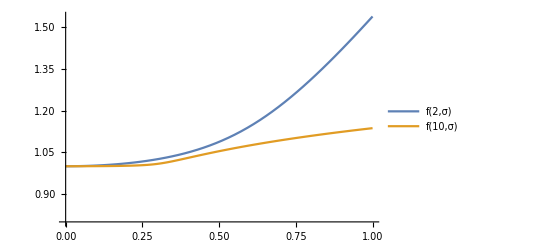

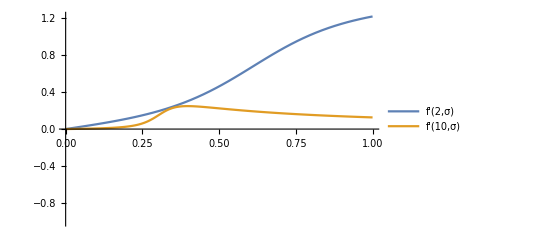

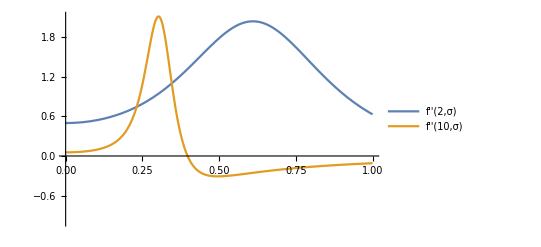

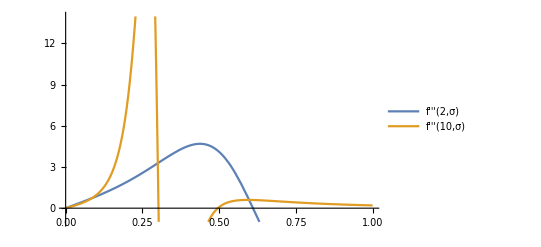

```mathematica
ClearAll["Global`*"]
f[m_,σ_]:=(((1+m*σ^2)+√((m*σ^2-1)^2+2*σ^2))/2)^(1/(2m-2));
Plot[{f[2,σ],f[10,σ]},{σ,0,1},PlotLegends->"Expressions",PlotRange->{0.8,Automatic}]
Plot[Evaluate@{D[f[2,σ],σ],D[f[10,σ],σ]},{σ,0,1},PlotLegends->{"f'(2,σ)","f'(10,σ)"},PlotRange->{-1,Automatic}]
Plot[Evaluate@{D[f[2,σ],{σ,2}],D[f[10,σ],{σ,2}]},{σ,0,1},PlotLegends->{"f''(2,σ)","f''(10,σ)"},PlotRange->{-1,Automatic}]
Plot[Evaluate@{D[f[2,σ],{σ,3}],D[f[10,σ],{σ,3}]},{σ,0,1},PlotLegends->{"f'''(2,σ)","f'''(10,σ)"},PlotRange->{-1,Automatic}]
```

```mathematica
FuncFunc[σ_]:= σ^3;
FuncFuncF[σ_]:= D[FuncFunc[σ],σ];
Solution = NSolve[FuncFuncF[σ]==0 ,σ]
```

{{σ→0.},{σ→0.}}

```mathematica
ns = 1.13; nsrun = -0.055;
R = 4.7*10^-5;
Func[ns_, nsrun_, m_,σ_,R_]:= 2*xiprecise[ns, nsrun, m,σ,R]+nsrun;
mmax = 10;
sigtable = Table[1,{i,2,mmax+1}];

For[m=2,m<mmax + 2,m++,
Solution = NSolve[Func[ns, nsrun, m,σ,R]==0 && 1>σ>0,σ];
Print["m = ", m , ", Solution = ", Solution];
sigtable[[m-1]]*=(σ/.Solution[[1]]) ;
Print["sigtable[[m-1]] = ",sigtable[[m-1]]];
sigmatildetable=MapIndexed[{#2[[1]]+1,#1}&,sigtable];
]
```

m = 2, Solution = {{σ→0.274165},{σ→0.34579}}

sigtable[[m-1]] = 0.274165

m = 3, Solution = {{σ→0.264334},{σ→0.344051}}

sigtable[[m-1]] = 0.264334

m = 4, Solution = {{σ→0.254707},{σ→0.347657}}

sigtable[[m-1]] = 0.254707

m = 5, Solution = {{σ→0.246153},{σ→0.352345}}

sigtable[[m-1]] = 0.246153

m = 6, Solution = {{σ→0.238415},{σ→0.35758}}

sigtable[[m-1]] = 0.238415

m = 7, Solution = {{σ→0.231259},{σ→0.363499}}

sigtable[[m-1]] = 0.231259

m = 8, Solution = {{σ→0.22453},{σ→0.369742}}

sigtable[[m-1]] = 0.22453

m = 9, Solution = {{σ→0.218127},{σ→0.375279}}

sigtable[[m-1]] = 0.218127

m = 10, Solution = {{σ→0.211984},{σ→0.379919}}

sigtable[[m-1]] = 0.211984

m = 11, Solution = {{σ→0.206061},{σ→0.384151}}

sigtable[[m-1]] = 0.206061

## Calculating potential variables from observation variables (FINAL FINAL)

### Previous Research (WMAP)

```mathematica
ClearAll["Global`*"]
(*Case1: VH2 and VH3*)
(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24(3m-1)*(m-1)*nsrun))^(1/4)
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))
(*mu*)
mu[ns_ , nsrun_, m_ ,R_]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))
(*M*)
M[ns_ , nsrun_, m_,R_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m, R] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_, R_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m, R ]*(M[ns , nsrun, m, R])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_,R_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_, R_] := 2(mu[ns , nsrun, m , R]*M[ns , nsrun, m, R]^(m-1))^(1/m);

psiinfmin[ns_ , nsrun_, m_, R_,σ_] :=(4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/σ)^(1/(m-1));
VH[ns_ , nsrun_, m_, σ_, R_]:= ( -mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)) )^2 * (1+σ^4/8+(psiinfmin[ns , nsrun, m, R,σ])^2/2)+ ((m^2*σ^2*(psiinfmin[ns , nsrun, m, R,σ])^2)/4^(2m-1))*(psiinfmin[ns , nsrun, m, R,σ]/M[ns , nsrun, m, R])^(4m-4) + ((m * (psiinfmin[ns , nsrun, m, R,σ])^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2)) ); 
VHExact[ns_ , nsrun_, m_, σ_, R_]:=　Exp[ σ^2/2+(psiinfmin[ns , nsrun, m, R,σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfmin[ns , nsrun, m, R,σ])^(2m-1)/M[ns , nsrun, m, R]^(2(m-1))+psiinfmin[ns , nsrun, m, R,σ]/2*(-mu[ns , nsrun, m , R]^2+ (psiinfmin[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))))^2);
VH023[ns_ , nsrun_, m_, σ_, R_]:= mu[ns , nsrun, m , R]^4+ mu[ns , nsrun, m , R]^4*σ^4/8-2*mu[ns , nsrun, m , R]^2* psiinfmin[ns , nsrun, m, R, σ]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*σ^2*psiinfmin[ns , nsrun, m, R, σ]^2)/4^(2m-1))*(psiinfmin[ns , nsrun, m, R, σ]/M[ns , nsrun, m, R])^(4m-4) ;

NrPotInt[ns_ , nsrun_, m_, R_] := NIntegrate[VH[ns , nsrun, m, σ, R]/D[VH[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotIntExact[ns_ , nsrun_, m_, R_] := NIntegrate[VHExact[ns , nsrun, m, σ, R]/D[VHExact[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotInt023[ns_ , nsrun_, m_, R_] := NIntegrate[VH023[ns , nsrun, m, σ, R]/D[VH023[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];

NrEst1[ns_ , nsrun_, m_, R_] := If[sigma[ns , nsrun, m ]> sigmad[ns , nsrun, m ],
								((3m-2)/(2m-1))*1/(sigmad[ns , nsrun, m ])^2-1/(sigma[ns , nsrun, m ])^2,
								((m-1)/(2m-1))*1/(sigmad[ns , nsrun, m ])^2*(sigma[ns , nsrun, m ]/sigmad[ns , nsrun, m ])^((4m-2)/(m-1))];
NrEst2[ns_ , nsrun_] := 1/(sigmad[ns , nsrun, 2 ])^2((Pi-Log[3+Sqrt[2]])/(4*Sqrt[2])-1+sigma[ns , nsrun, 2 ]/sigmad[ns , nsrun, 2 ]);

termsubtract[ns_ , nsrun_, m_ , R_]:=VHExact[ns , nsrun, m, sigma[ns , nsrun, m ], R] - mu[ns , nsrun, m , R]^4;
term0[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*sigma[ns , nsrun, m ]^4/8;
term1[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistart[ns, nsrun, m ,R]^2/2;
term2[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4[ns_ , nsrun_, m_ , R_] := Abs[((m * psistart[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistart[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistart[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * psistart[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2)];
term1div[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistart[ns, nsrun, m ,R];
term2div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistart[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3div[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistart[ns, nsrun, m ,R])/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistart[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistart[ns, nsrun, m ,R])/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4div[ns_ , nsrun_, m_ , R_] := Abs[((m * (2m)*psistart[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234div[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistart[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistart[ns, nsrun, m ,R])/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistart[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term1234div[ns_ , nsrun_, m_ , R_] := Abs[mu[ns , nsrun, m , R]^4*psistart[ns, nsrun, m ,R]-2*mu[ns , nsrun, m , R]^2* (2m*psistart[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistart[ns, nsrun, m ,R])/4^(2m-1))*(psistart[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistart[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];

(*Case2: VH1, VH2, VH3 and VH4*)
f[m_,σ_]:=(((1+m*σ^2)+√((m*σ^2-1)^2+2*σ^2))/2)^(1/(2m-2));
g[m_,σ_]:= 1/σ^(2/(m-1))((f[m,σ])^2/2-(f[m,σ])^(2m)/(m(2m-1)σ^2)+(f[m,σ])^(4m-2)/((2m-1)^2 σ^2)-(f[m,σ])^(2m)/(2m-1));
psistartprecise[ns_ , nsrun_, m_,R_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/sigma[ns , nsrun, m ])^(1/(m-1))*(((1+m*sigma[ns , nsrun, m ]^2)+√((m*sigma[ns , nsrun, m ]^2-1)^2+2*sigma[ns , nsrun, m ]^2))/2)^(1/(2m-2));
psiinfminprecise[ns_ , nsrun_, m_, R_,σ_] := (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m, R]*(mu[ns, nsrun, m, R]/σ)^(1/(m-1))*(((1+m*σ^2)+√((m*σ^2-1)^2+2*σ^2))/2)^(1/(2m-2));

VHpsiprecise[ns_ , nsrun_, m_, σ_, R_]:= ( -mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)) )^2 * (1+σ^4/8+(psiinfminprecise[ns , nsrun, m, R,σ])^2/2)+ ((m^2*σ^2*(psiinfminprecise[ns , nsrun, m, R,σ])^2)/4^(2m-1))*(psiinfminprecise[ns , nsrun, m, R,σ]/M[ns , nsrun, m, R])^(4m-4) + ((m * (psiinfminprecise[ns , nsrun, m, R,σ])^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2)) ); 
VHExactpsiprecise[ns_ , nsrun_, m_, σ_, R_]:=　Exp[ σ^2/2+(psiinfminprecise[ns , nsrun, m, R,σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfminprecise[ns , nsrun, m, R,σ])^(2m-1)/M[ns , nsrun, m, R]^(2(m-1))+psiinfminprecise[ns , nsrun, m, R,σ]/2*(-mu[ns , nsrun, m , R]^2+ (psiinfminprecise[ns , nsrun, m, R,σ])^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))))^2);

VH01234[ns_ , nsrun_, m_, σ_, R_]:= mu[ns , nsrun, m , R]^4+ mu[ns , nsrun, m , R]^4*σ^4/8+mu[ns , nsrun, m , R]^4*psiinfminprecise[ns , nsrun, m, R, σ]^2/2-2*mu[ns , nsrun, m , R]^2* psiinfminprecise[ns , nsrun, m, R, σ]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*σ^2*psiinfminprecise[ns , nsrun, m, R, σ]^2)/4^(2m-1))*(psiinfminprecise[ns , nsrun, m, R, σ]/M[ns , nsrun, m, R])^(4m-4)+((m * psiinfminprecise[ns , nsrun, m, R, σ]^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 );
xiprecise[ns_ , nsrun_, m_, σ_, R_]:= (Derivative[0,0,0,3,0][VH01234][ns , nsrun, m, σ, R]* Derivative[0,0,0,1,0][VH01234][ns , nsrun, m, σ, R])/(mu[ns , nsrun, m , R]^4)^2


NrPotIntpsiprecise[ns_ , nsrun_, m_, R_] := NIntegrate[VHpsiprecise[ns , nsrun, m, σ, R]/D[VHpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];
NrPotIntExactpsiprecise[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigmac[ns , nsrun, m, R ],sigma[ns , nsrun, m ]}];



termsubtractprecise[ns_ , nsrun_, m_ , R_]:=VHExact[ns , nsrun, m, sigma[ns , nsrun, m ], psistartprecise[ns, nsrun, m ,R], R] - mu[ns , nsrun, m , R]^4;
term0precise[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*sigma[ns , nsrun, m ]^4/8;
term1precise[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R]^2/2;
term2precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3precise[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4precise[ns_ , nsrun_, m_ , R_] := Abs[((m * psistartprecise[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234precise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* psistartprecise[ns, nsrun, m ,R]^(2m)/(4^m*M[ns , nsrun, m, R]^(2m-2))+((m^2*sigma[ns , nsrun, m ]^2*psistartprecise[ns, nsrun, m ,R]^2)/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * psistartprecise[ns, nsrun, m ,R]^(2m) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2)];


term1divprecise[ns_ , nsrun_, m_ , R_] := mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R];
term2divprecise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))];
term3divprecise[ns_ , nsrun_, m_ , R_] := ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4);
term23divprecise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)];
term4divprecise[ns_ , nsrun_, m_ , R_] := Abs[((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term234divprecise[ns_ , nsrun_, m_ , R_] := Abs[-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
term1234divprecise[ns_ , nsrun_, m_ , R_] := Abs[mu[ns , nsrun, m , R]^4*psistartprecise[ns, nsrun, m ,R]-2*mu[ns , nsrun, m , R]^2* (2m*psistartprecise[ns, nsrun, m ,R]^(2m-1))/(4^m*M[ns , nsrun, m, R]^(2m-2))+ ((m^2*sigma[ns , nsrun, m ]^2*(4m-2)*psistartprecise[ns, nsrun, m ,R])/4^(2m-1))*(psistartprecise[ns, nsrun, m ,R]/M[ns , nsrun, m, R])^(4m-4)+((m * (2m)*psistartprecise[ns, nsrun, m ,R]^(2m-1) * sigma[ns , nsrun, m ]^2)/(2^(2m-1)*M[ns , nsrun, m, R]^(2m-2)))*(-mu[ns , nsrun, m, R ]^2 )];
```

```mathematica
ns = 1.13; nsrun = -0.055;R = 4.7*10^-5;
(*ns = 0.9649; nsrun = −0.0045;*)
mmaxp = 6; 
sigtable = Table[1,{i,2,mmaxp+1}];
sigdtable = Table[1,{i,2,mmaxp+1}];
sigctable = Table[1,{i,2,mmaxp+1}];
Atable= Table[1,{i,2,mmaxp+1}];
muptable= Table[1,{i,2,mmaxp+1}];
Mptable = Table[1,{i,2,mmaxp+1}];
psistartptable= Table[1,{i,2,mmaxp+1}];
psiendptable= Table[1,{i,2,mmaxp+1}];
NrPotIntExactpsiptable= Table[1,{i,2,mmaxp+1}];
NrPotInt01234psiptable = Table[1,{i,2,mmaxp+1}];

Func[ns_, nsrun_, m_,σ_]:=(3*σ*Derivative[0,2][g][ m, σ]+ (ns-1-3 σ^2)/2 Derivative[0,3][g][ m, σ])* (σ^3*Derivative[0,2][g][ m, σ]
+(ns-1-3 σ^2)*Derivative[0,1][g][ m, σ] )+(Derivative[0,2][g][ m, σ])^2*nsrun ;


For[m=2,m<mmaxp + 2,m++,
Solution = NSolve[Func[ns, nsrun, m,σ]==0  && 0<σ < 1 ,σ];
Print["m = ", m , ", Solution = ", Solution];
sigtable[[m-1]]*=(σ/.Solution[[1]]) ;

Atable[[m-1]]*= (ns-1-3 sigtable[[m-1]]^2)/2*1/(Derivative[0,2][g][ m, σ]/.σ ->sigtable[[m-1]]);
Print["sigtable[[m-1]] = ",sigtable[[m-1]]];
Print["Atable[[m-1]] = ",Atable[[m-1]]];
sigmatildetable=MapIndexed[{#2[[1]]+1,#1}&,sigtable];

Solutionsigmad = NSolve[σ^3/2 - Atable[[m-1]]*Derivative[0,1][g][ m, σ]==0  && 0<σ < 1 ,σ];
Solutionsigmac = NSolve[(3 σ^2)/2+Atable[[m-1]]*Derivative[0,2][g][ m, σ]+1==0  && 0<σ < 1 ,σ];

sigdtable[[m-1]]*=(σ/.Solutionsigmad[[1]]) ;
Print["sigdtable[[m-1]] = ",sigdtable[[m-1]]];

sigctable[[m-1]]*=(σ/.Solutionsigmac[[1]]) ;
Print["sigctable[[m-1]] = ",sigctable[[m-1]]];
sigmadtildetable=MapIndexed[{#2[[1]]+1,#1}&,sigdtable];
sigmactildetable=MapIndexed[{#2[[1]]+1,#1}&,sigctable];

muptable[[m-1]]*=√(√3*Pi*R*( sigtable[[m-1]]^3+2*Atable[[m-1]]*(Derivative[0,1][g][ m, σ]/.σ ->sigtable[[m-1]])));
  Mptable[[m-1]]*= (√Atable[[m-1]])/((muptable[[m-1]])^(1/(m-1))*(4^m/((2m-1)*(2m)))^(1/(2m-2)));
Print["muptable[[m-1]] = ",muptable[[m-1]]];
Print["Mptable[[m-1]] = ",Mptable[[m-1]]];
muptildetable=MapIndexed[{#2[[1]]+1,#1}&,muptable];
Mptildetable=MapIndexed[{#2[[1]]+1,#1}&,Mptable];


psistartptable[[m-1]] *= (4^m/((2m-1)*(2m)))^(1/(2m-2))*Mptable[[m-1]]*(muptable[[m-1]]/sigtable[[m-1]])^(1/(m-1))*f[m,sigtable[[m-1]]];
Print["psistartptable[[m-1]] = ",psistartptable[[m-1]]];
psistarttildetable=MapIndexed[{#2[[1]]+1,#1}&,psistartptable];

psiendptable[[m-1]] *=  2(muptable[[m-1]]*Mptable[[m-1]]^(m-1))^(1/m);
Print["psiendptable[[m-1]] = ",psiendptable[[m-1]]];

psiendtildetable=MapIndexed[{#2[[1]]+1,#1}&,psiendptable];

psiinfminp[m_, σ_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*Mptable[[m-1]]*(muptable[[m-1]]/σ)^(1/(m-1))*f[m,σ];

VHExactpsip[m_, σ_]:=　Exp[ σ^2/2+(psiinfminp[m, σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-muptable[[m-1]]^2+ (psiinfminp[m, σ])^(2m)/(4^m*Mptable[[m-1]]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfminp[m, σ])^(2m-1)/Mptable[[m-1]]^(2(m-1))+psiinfminp[m, σ]/2*(-muptable[[m-1]]^2+ (psiinfminp[m, σ])^(2m)/(4^m*Mptable[[m-1]]^(2m-2))))^2);
NrPotIntExactpsip[m_] := NIntegrate[VHExactpsip[m, σ]/D[VHExactpsip[m, σ],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotIntExactpsiptable[[m-1]] *= NrPotIntExactpsip[m];
Print["NrPotIntExactpsiptable[[m-1]] = ",NrPotIntExactpsiptable[[m-1]]];

NrPotIntExactpsiptildetable=MapIndexed[{#2[[1]]+1,#1}&,NrPotIntExactpsiptable];


VH01234psip[m_, σ_]:=　muptable[[m-1]]^4+ muptable[[m-1]]^4*σ^4/8+muptable[[m-1]]^4*psiinfminp[m, σ]^2/2-2*muptable[[m-1]]^2* psiinfminp[m, σ]^(2m)/(4^m*Mptable[[m-1]]^(2m-2))+((m^2*σ^2*psiinfminp[m, σ]^2)/4^(2m-1))*(psiinfminp[m, σ]/Mptable[[m-1]])^(4m-4)+((m * psiinfminp[m, σ]^(2m) * σ^2)/(2^(2m-1)*Mptable[[m-1]]^(2m-2)))*(-muptable[[m-1]]^2 );
NrPotInt01234psip[m_] := NIntegrate[VH01234psip[m, σ]/D[VH01234psip[m, σ],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotInt01234psiptable[[m-1]] *= NrPotInt01234psip[m];
Print["NrPotInt01234psiptable[[m-1]] = ",NrPotInt01234psiptable[[m-1]]];

NrPotInt01234psiptildetable=MapIndexed[{#2[[1]]+1,#1}&,NrPotInt01234psiptable];


]
```

m = 2, Solution = {{σ→0.280034},{σ→0.88554}}

sigtable[[m-1]] = 0.280034

Atable[[m-1]] = 0.0000245733

sigdtable[[m-1]] = 0.237134

sigctable[[m-1]] = 0.171515

muptable[[m-1]] = 0.00265457

Mptable[[m-1]] = 1.61722

psistartptable[[m-1]] = 0.0180888

psiendptable[[m-1]] = 0.131042

NrPotIntExactpsiptable[[m-1]] = 6.64484

NrPotInt01234psiptable[[m-1]] = 6.73066

m = 3, Solution = {{σ→0.283032},{σ→0.62435}}

sigtable[[m-1]] = 0.283032

Atable[[m-1]] = 0.000368174

sigdtable[[m-1]] = 0.240187

sigctable[[m-1]] = 0.16092

muptable[[m-1]] = 0.00272701

Mptable[[m-1]] = 0.304032

psistartptable[[m-1]] = 0.0365052

psiendptable[[m-1]] = 0.126339

NrPotIntExactpsiptable[[m-1]] = 6.93826

NrPotInt01234psiptable[[m-1]] = 7.08701

m = 4, Solution = {{σ→0.285061},{σ→0.508474}}

sigtable[[m-1]] = 0.285061

Atable[[m-1]] = 0.00138316

sigdtable[[m-1]] = 0.240439

sigctable[[m-1]] = 0.158738

muptable[[m-1]] = 0.0027258

Mptable[[m-1]] = 0.206663

psistartptable[[m-1]] = 0.0570219

psiendptable[[m-1]] = 0.140072

NrPotIntExactpsiptable[[m-1]] = 7.0288

NrPotInt01234psiptable[[m-1]] = 7.27362

m = 5, Solution = {{σ→0.287515},{σ→0.438087}}

sigtable[[m-1]] = 0.287515

Atable[[m-1]] = 0.00345534

sigdtable[[m-1]] = 0.239806

sigctable[[m-1]] = 0.160076

muptable[[m-1]] = 0.00269451

Mptable[[m-1]] = 0.190379

psistartptable[[m-1]] = 0.0808957

psiendptable[[m-1]] = 0.162488

NrPotIntExactpsiptable[[m-1]] = 7.02454

NrPotInt01234psiptable[[m-1]] = 7.43945

m = 6, Solution = {{σ→0.291256},{σ→0.38766}}

sigtable[[m-1]] = 0.291256

Atable[[m-1]] = 0.00737426

sigdtable[[m-1]] = 0.2391

sigctable[[m-1]] = 0.164365

muptable[[m-1]] = 0.0026378

Mptable[[m-1]] = 0.199725

psistartptable[[m-1]] = 0.110699

psiendptable[[m-1]] = 0.194207

NrPotIntExactpsiptable[[m-1]] = 6.91036

NrPotInt01234psiptable[[m-1]] = 7.63767

m = 7, Solution = {{σ→0.299088},{σ→0.344899}}

sigtable[[m-1]] = 0.299088

Atable[[m-1]] = 0.0160079

sigdtable[[m-1]] = 0.239871

sigctable[[m-1]] = 0.174373

muptable[[m-1]] = 0.00253682

Mptable[[m-1]] = 0.235463

psistartptable[[m-1]] = 0.155894

psiendptable[[m-1]] = 0.246526

NrPotIntExactpsiptable[[m-1]] = 6.53859

NrPotInt01234psiptable[[m-1]] = 7.95916

```mathematica
sigmatildetable
sigmadtildetable
sigmactildetable
muptildetable
Mptildetable
psistarttildetable
psiendtildetable
NrPotIntExactpsiptildetable
NrPotInt01234psiptildetable
```

{{2,0.280034},{3,0.283032},{4,0.285061},{5,0.287515},{6,0.291256},{7,0.299088}}

{{2,0.237134},{3,0.240187},{4,0.240439},{5,0.239806},{6,0.2391},{7,0.239871}}

{{2,0.171515},{3,0.16092},{4,0.158738},{5,0.160076},{6,0.164365},{7,0.174373}}

{{2,0.00265457},{3,0.00272701},{4,0.0027258},{5,0.00269451},{6,0.0026378},{7,0.00253682}}

{{2,1.61722},{3,0.304032},{4,0.206663},{5,0.190379},{6,0.199725},{7,0.235463}}

{{2,0.0180888},{3,0.0365052},{4,0.0570219},{5,0.0808957},{6,0.110699},{7,0.155894}}

{{2,0.131042},{3,0.126339},{4,0.140072},{5,0.162488},{6,0.194207},{7,0.246526}}

{{2,6.64484},{3,6.93826},{4,7.0288},{5,7.02454},{6,6.91036},{7,6.53859}}

{{2,6.73066},{3,7.08701},{4,7.27362},{5,7.43945},{6,7.63767},{7,7.95916}}

```mathematica
ns = 1.13; nsrun = -0.055;
R = 4.7*10^-5; (*amplitude of curvature perturbation*)

mmax = 10;



mu2table = Table[{m,mu[ns , nsrun, m, R ]^2},{m,2,mmax+1}];
psi2mtable = Table[{m,psistart[ns, nsrun, m ,R]^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2))},{m,2,mmax+1}];
plot0 = ListLogPlot[{mu2table,psi2mtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},Automatic},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"μ^2","(ψ_*)^(2  m)/4^m"},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];



term0table = Table[{m,term0[ns , nsrun, m , R]},{m,2,mmax+1}];
term1table = Table[{m,term1[ns , nsrun, m , R]},{m,2,mmax+1}];
term2table = Table[{m,term2[ns , nsrun, m , R]},{m,2,mmax+1}];
term3table = Table[{m,term3[ns , nsrun, m , R]},{m,2,mmax+1}];
term23table = Table[{m,term23[ns , nsrun, m , R]},{m,2,mmax+1}];
term4table = Table[{m,term4[ns , nsrun, m , R]},{m,2,mmax+1}];
term234table = Table[{m,term234[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtracttable = Table[{m,termsubtract[ns , nsrun, m , R]},{m,2,mmax+1}];
(*term5table = Table[{m,term5[ns , nsrun, m , R]},{m,2,mmax+1}];
term6table = Table[{m,term6[ns , nsrun, m , R]},{m,2,mmax+1}];*)
plot1 = ListLogPlot[{term0table,term1table,term2table,term3table,term4table,termsubtracttable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{Automatic,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"V_H0","V_H1","|V_H2|","V_H3","|V_H4|","|V_H-μ^4|"},LegendLayout->"Row"],{Right, Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

sigmatable = Table[{m,sigma[ns, nsrun, m ]},{m,2,mmax+1}];
sigmadtable = Table[{m,sigmad[ns, nsrun, m ]},{m,2,mmax+1}];
sigmactable = Table[{m,sigmac[ns, nsrun, m ,R]},{m,2,mmax+1}];

(*Func[ns_, nsrun_, m_,σ_]:=
(-((2m-1)(2m-3)(m+1)m)/(2(m-1)^2(3m-1))(3 σ^2-ns+1)+(2m-1)/((m-1)σ)(3 σ^2-ns+1)+3σ)*(-((2m-1)(2m-3))/(2(3m-1))(3 σ^2-ns+1)σ^3+(m-1)/(3m-1)(3 σ^2-ns+1)σ+σ^3)+nsrun*)


plot2 = ListPlot[{sigmatable,sigmadtable,sigmactable,sigmatildetable,sigmadtildetable,sigmactildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"σ_*","σ_d","σ_c","(σ̃)_*","(σ̃)_d","(σ̃)_c"},LegendLayout->"Row"],{Right, Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


mutable = Table[{m,mu[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot3 =ListPlot[{mutable,muptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{μ,μ̃},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

Mtable = Table[{m,M[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot4 =ListPlot[{Mtable,Mptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,1.8}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{M,M̃},{Right,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotInt023table = Table[{m,NrPotInt023[ns, nsrun, m,R ]},{m,2,mmax+1}];
(*NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntPsiptable = Table[{m,NrPotIntpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExactPsiptable = Table[{m,NrPotIntExactpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
*)
NrEst1table = Table[{m,NrEst1[ns , nsrun, m ,R]},{m,2,mmax+1}];
NrEst2table= {{2,NrEst2[ns, nsrun]}};

(*NrPotIntExactpsiprecisetildesigma[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotIntExactPsipSigmaptable= Table[{m,NrPotIntExactpsiprecisetildesigma[ns, nsrun, m,R ]},{m,2,mmaxp+1}];*)


plot5 =ListPlot[{NrEst1table,NrEst2table,NrPotIntExacttable,NrPotIntExactpsiptildetable,NrPotInt023table,NrPotInt01234psiptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"N_Hest1","N_Hest2","N_HV_Exact","(Ñ)_HV_Exact","N_HV_023","(Ñ)_HV_01234"},LegendLayout->"Row"],{Right,Bottom}],LabelStyle->Directive[Black],Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


psistarttable = Table[{m,psistart[ns, nsrun, m ,R]},{m,2,mmax+1}];

(*psistartprecisetable = Table[{m,psistartprecise[ns , nsrun, m,R]},{m,2,mmax+1}];*)
psiendtable = Table[{m,psiend[ns, nsrun, m ,R]},{m,2,mmax+1}];
plot6 =ListPlot[{psistarttable,psistarttildetable,psiendtable,psiendtildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"ψ_*","(ψ̃)_*","ψ_oscend","(ψ̃)_oscend"},{Left,Top}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


term1divtable = Table[{m,term1div[ns , nsrun, m , R]},{m,2,mmax+1}];
term2divtable = Table[{m,term2div[ns , nsrun, m , R]},{m,2,mmax+1}];
term3divtable = Table[{m,term3div[ns , nsrun, m , R]},{m,2,mmax+1}];
term23divtable = Table[{m,term23div[ns , nsrun, m , R]},{m,2,mmax+1}];
term4divtable = Table[{m,term4div[ns , nsrun, m , R]},{m,2,mmax+1}];
term234divtable = Table[{m,term234div[ns , nsrun, m , R]},{m,2,mmax+1}];
term1234divtable =  Table[{m,term1234div[ns , nsrun, m , R]},{m,2,mmax+1}];
plot7 = ListLogPlot[{term1divtable,term2divtable,term3divtable,term4divtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotStyle->{Automatic,Automatic,Directive[Dashed],Automatic},PlotLegends->Placed[{"V_ψ_H1","|V_ψ_H2|","V_ψ_H3","|V_ψ_H4|"},{Right,Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


term0precisetable = Table[{m,term0precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term1precisetable = Table[{m,term1precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term2precisetable = Table[{m,term2precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term3precisetable = Table[{m,term3precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term23precisetable = Table[{m,term23precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term4precisetable = Table[{m,term4precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term234precisetable = Table[{m,term234precise[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtractprecisetable = Table[{m,termsubtractprecise[ns , nsrun, m , R]},{m,2,mmax+1}];


(*term1divtable,term2divtable,term3divtable,term4divtable,term23divtable,term234divtable ,"V'_H1","|V'_H2|","V'_H3","|V'_H4|","V'_H3","|V'_H4|","|V'_H2+V'_H3|","|V'_H2+V'_H3+V'_H4|"*)
plots={{plot0,plot1},{plot7,plot2},{plot3,plot4},{plot6,plot5}};
Result =ResourceFunction["PlotGrid"][plots,FrameStyle->Black, ImageSize->{900,900}]
Export["SHI_m_WMAP.eps",Result]
```

-Graphics-

SHI_m_WMAP.eps

```mathematica
ns = 1.13; nsrun = -0.055;m =2;R = 4.7*10^-5;
Print["σ_* = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m,R]", (σ̃)_* =  ",sigtable[[m-1]]", (σ̃)_d = ",sigdtable[[m-1]]", (σ̃)_c = ",sigctable[[m-1]]]
Print["μ = ",mu[ns , nsrun, m,R ]", M = ",M[ns , nsrun, m,R ]", μ̃ = ",muptable[[m-1]]", M̃ = ",Mptable[[m-1]]]
Print["ψ_*= ",psistart[ns , nsrun, m,R]", (ψ̃)_* = ",psistartptable[[m-1]]", ψ_oscend = ",psiend[ns , nsrun, m,R], ", (ψ̃)_oscend = ",psiendptable[[m-1]]]
Print["N_Hest1 = ",NrEst1[ns , nsrun, m ,R]", N_Hest2 = ",NrEst2[ns , nsrun],", N_HV_Exact = ",NrPotIntExact[ns , nsrun, m,R ],", (Ñ)_HV_Exact = ",NrPotIntExactpsiptable[[m-1]],", N_HV_023 = ",NrPotInt023[ns , nsrun, m,R ],", (Ñ)_HV_01234 = ",NrPotInt01234psiptable[[m-1]] ]
```

σ_* = 0.280196 , σ_d = 0.237765 , σ_c = 0.171601 , (σ̃)_* =  0.280034 , (σ̃)_d = 0.237134 , (σ̃)_c = 0.171515

μ = 0.00267178 , M = 1.55386 , μ̃ = 0.00265457 , M̃ = 1.61722

ψ_*= 0.0171088 , (ψ̃)_* = 0.0180888 , ψ_oscend = 0.128865, (ψ̃)_oscend = 0.131042

N_Hest1 = 10.8482 , N_Hest2 = 8.33751, N_HV_Exact = 6.8853, (Ñ)_HV_Exact = 6.64484, N_HV_023 = 6.69981, (Ñ)_HV_01234 = 6.73066

### Planck data

```mathematica
ns = 0.9649; nsrun = −0.0045;
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rmeanvalue = (Rmean/.Rmeansol)[[1]];
R = Rmeanvalue; (*amplitude of curvature perturbation*)
(*ns = 0.9649; nsrun = −0.0045;*)
mmaxp = 30; 
sigtable = Table[1,{i,2,mmaxp+1}];
sigdtable = Table[1,{i,2,mmaxp+1}];
sigctable = Table[1,{i,2,mmaxp+1}];
Atable= Table[1,{i,2,mmaxp+1}];
muptable= Table[1,{i,2,mmaxp+1}];
Mptable = Table[1,{i,2,mmaxp+1}];
psistartptable= Table[1,{i,2,mmaxp+1}];
psiendptable= Table[1,{i,2,mmaxp+1}];
NrPotIntExactpsiptable= Table[1,{i,2,mmaxp+1}];
NrPotInt01234psiptable= Table[1,{i,2,mmaxp+1}];


Func[ns_, nsrun_, m_,σ_]:=(3*σ*Derivative[0,2][g][ m, σ]+ (ns-1-3 σ^2)/2 Derivative[0,3][g][ m, σ])* (σ^3*Derivative[0,2][g][ m, σ]
+(ns-1-3 σ^2)*Derivative[0,1][g][ m, σ] )+(Derivative[0,2][g][ m, σ])^2*nsrun ;


For[m=2,m<mmaxp + 2,m++,
Solution = NSolve[Func[ns, nsrun, m,σ]==0  && 0<σ < 1 ,σ];
Print["m = ", m , ", Solution = ", Solution];
sigtable[[m-1]]*=(σ/.Solution[[1]]) ;

Atable[[m-1]]*= (ns-1-3 sigtable[[m-1]]^2)/2*1/(Derivative[0,2][g][ m, σ]/.σ ->sigtable[[m-1]]);
Print["sigtable[[m-1]] = ",sigtable[[m-1]]];
Print["Atable[[m-1]] = ",Atable[[m-1]]];
sigmatildetable=MapIndexed[{#2[[1]]+1,#1}&,sigtable];

Solutionsigmad = NSolve[σ^3/2 - Atable[[m-1]]*Derivative[0,1][g][ m, σ]==0  && 0<σ < 1 ,σ];
Solutionsigmac = NSolve[(3 σ^2)/2+Atable[[m-1]]*Derivative[0,2][g][ m, σ]+1==0  && 0<σ < 1 ,σ];

sigdtable[[m-1]]*=(σ/.Solutionsigmad[[1]]) ;
Print["sigdtable[[m-1]] = ",sigdtable[[m-1]]];

sigctable[[m-1]]*=(σ/.Solutionsigmac[[1]]) ;
Print["sigctable[[m-1]] = ",sigctable[[m-1]]];
sigmadtildetable=MapIndexed[{#2[[1]]+1,#1}&,sigdtable];
sigmactildetable=MapIndexed[{#2[[1]]+1,#1}&,sigctable];

muptable[[m-1]]*=√(√3*Pi*R*( sigtable[[m-1]]^3+2*Atable[[m-1]]*(Derivative[0,1][g][ m, σ]/.σ ->sigtable[[m-1]])));
  Mptable[[m-1]]*= (√Atable[[m-1]])/((muptable[[m-1]])^(1/(m-1))*(4^m/((2m-1)*(2m)))^(1/(2m-2)));
Print["muptable[[m-1]] = ",muptable[[m-1]]];
Print["Mptable[[m-1]] = ",Mptable[[m-1]]];
muptildetable=MapIndexed[{#2[[1]]+1,#1}&,muptable];
Mptildetable=MapIndexed[{#2[[1]]+1,#1}&,Mptable];


psistartptable[[m-1]] *= (4^m/((2m-1)*(2m)))^(1/(2m-2))*Mptable[[m-1]]*(muptable[[m-1]]/sigtable[[m-1]])^(1/(m-1))*f[m,sigtable[[m-1]]];
Print["psistartptable[[m-1]] = ",psistartptable[[m-1]]];
psistarttildetable=MapIndexed[{#2[[1]]+1,#1}&,psistartptable];

psiendptable[[m-1]] *=  2(muptable[[m-1]]*Mptable[[m-1]]^(m-1))^(1/m);
Print["psiendptable[[m-1]] = ",psiendptable[[m-1]]];

psiendtildetable=MapIndexed[{#2[[1]]+1,#1}&,psiendptable];

psiinfminp[m_, σ_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*Mptable[[m-1]]*(muptable[[m-1]]/σ)^(1/(m-1))*f[m,σ];

VHExactpsip[m_, σ_]:=　Exp[ σ^2/2+(psiinfminp[m, σ])^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(-muptable[[m-1]]^2+ (psiinfminp[m, σ])^(2m)/(4^m*Mptable[[m-1]]^(2m-2)))^2+2*σ^2/2*(m/2^(2m-1)*(psiinfminp[m, σ])^(2m-1)/Mptable[[m-1]]^(2(m-1))+psiinfminp[m, σ]/2*(-muptable[[m-1]]^2+ (psiinfminp[m, σ])^(2m)/(4^m*Mptable[[m-1]]^(2m-2))))^2);
NrPotIntExactpsip[m_] := NIntegrate[VHExactpsip[m, σ]/D[VHExactpsip[m, σ],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotIntExactpsiptable[[m-1]] *= NrPotIntExactpsip[m];
Print["NrPotIntExactpsiptable[[m-1]] = ",NrPotIntExactpsiptable[[m-1]]];

NrPotIntExactpsiptildetable=MapIndexed[{#2[[1]]+1,#1}&,NrPotIntExactpsiptable];


VH01234psip[m_, σ_]:=　muptable[[m-1]]^4+ muptable[[m-1]]^4*σ^4/8+muptable[[m-1]]^4*psiinfminp[m, σ]^2/2-2*muptable[[m-1]]^2* psiinfminp[m, σ]^(2m)/(4^m*Mptable[[m-1]]^(2m-2))+((m^2*σ^2*psiinfminp[m, σ]^2)/4^(2m-1))*(psiinfminp[m, σ]/Mptable[[m-1]])^(4m-4)+((m * psiinfminp[m, σ]^(2m) * σ^2)/(2^(2m-1)*Mptable[[m-1]]^(2m-2)))*(-muptable[[m-1]]^2 );
NrPotInt01234psip[m_] := NIntegrate[VH01234psip[m, σ]/D[VH01234psip[m, σ],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotInt01234psiptable[[m-1]] *= NrPotInt01234psip[m];
Print["NrPotInt01234psiptable[[m-1]] = ",NrPotInt01234psiptable[[m-1]]];

NrPotInt01234psiptildetable=MapIndexed[{#2[[1]]+1,#1}&,NrPotInt01234psiptable];

]
```

m = 2, Solution = {{σ→0.0942888},{σ→0.876007}}

sigtable[[m-1]] = 0.0942888

Atable[[m-1]] = 1.96901×10^-8

sigdtable[[m-1]] = 0.0981675

sigctable[[m-1]] = 0.0528263

muptable[[m-1]] = 0.00070555

Mptable[[m-1]] = 0.172237

psistartptable[[m-1]] = 0.00149156

psiendptable[[m-1]] = 0.0220474

NrPotIntExactpsiptable[[m-1]] = 20.3954

NrPotInt01234psiptable[[m-1]] = 20.3719

m = 3, Solution = {{σ→0.0953548},{σ→0.613561}}

sigtable[[m-1]] = 0.0953548

Atable[[m-1]] = 7.81682×10^-7

sigdtable[[m-1]] = 0.102654

sigctable[[m-1]] = 0.0477493

muptable[[m-1]] = 0.000761841

Mptable[[m-1]] = 0.0265044

psistartptable[[m-1]] = 0.00286647

psiendptable[[m-1]] = 0.0162379

NrPotIntExactpsiptable[[m-1]] = 20.3412

NrPotInt01234psiptable[[m-1]] = 20.3398

m = 4, Solution = {{σ→0.0956898},{σ→0.498076}}

sigtable[[m-1]] = 0.0956898

Atable[[m-1]] = 3.75785×10^-6

sigdtable[[m-1]] = 0.104409

sigctable[[m-1]] = 0.0457

muptable[[m-1]] = 0.000783152

Mptable[[m-1]] = 0.0163247

psistartptable[[m-1]] = 0.00424153

psiendptable[[m-1]] = 0.0152801

NrPotIntExactpsiptable[[m-1]] = 20.3175

NrPotInt01234psiptable[[m-1]] = 20.3261

m = 5, Solution = {{σ→0.0959422},{σ→0.429449}}

sigtable[[m-1]] = 0.0959422

Atable[[m-1]] = 9.82821×10^-6

sigdtable[[m-1]] = 0.105321

sigctable[[m-1]] = 0.0446651

muptable[[m-1]] = 0.000793973

Mptable[[m-1]] = 0.0137809

psistartptable[[m-1]] = 0.00563631

psiendptable[[m-1]] = 0.0155745

NrPotIntExactpsiptable[[m-1]] = 20.3153

NrPotInt01234psiptable[[m-1]] = 20.3322

m = 6, Solution = {{σ→0.0961912},{σ→0.382658}}

sigtable[[m-1]] = 0.0961912

Atable[[m-1]] = 0.0000195029

sigdtable[[m-1]] = 0.10586

sigctable[[m-1]] = 0.0440902

muptable[[m-1]] = 0.000800231

Mptable[[m-1]] = 0.0130385

psistartptable[[m-1]] = 0.00705723

psiendptable[[m-1]] = 0.0163778

NrPotIntExactpsiptable[[m-1]] = 20.3249

NrPotInt01234psiptable[[m-1]] = 20.3505

m = 7, Solution = {{σ→0.0964522},{σ→0.348094}}

sigtable[[m-1]] = 0.0964522

Atable[[m-1]] = 0.0000331691

sigdtable[[m-1]] = 0.106203

sigctable[[m-1]] = 0.0437644

muptable[[m-1]] = 0.000804083

Mptable[[m-1]] = 0.0129804

psistartptable[[m-1]] = 0.00850798

psiendptable[[m-1]] = 0.0174481

NrPotIntExactpsiptable[[m-1]] = 20.3413

NrPotInt01234psiptable[[m-1]] = 20.3769

m = 8, Solution = {{σ→0.0967288},{σ→0.321181}}

sigtable[[m-1]] = 0.0967288

Atable[[m-1]] = 0.0000511812

sigdtable[[m-1]] = 0.10643

sigctable[[m-1]] = 0.0435907

muptable[[m-1]] = 0.000806503

Mptable[[m-1]] = 0.0132571

psistartptable[[m-1]] = 0.00999152

psiendptable[[m-1]] = 0.0186853

NrPotIntExactpsiptable[[m-1]] = 20.3617

NrPotInt01234psiptable[[m-1]] = 20.409

m = 9, Solution = {{σ→0.097022},{σ→0.299427}}

sigtable[[m-1]] = 0.097022

Atable[[m-1]] = 0.0000738989

sigdtable[[m-1]] = 0.106583

sigctable[[m-1]] = 0.0435182

muptable[[m-1]] = 0.000807995

Mptable[[m-1]] = 0.0137275

psistartptable[[m-1]] = 0.0115106

psiendptable[[m-1]] = 0.0200417

NrPotIntExactpsiptable[[m-1]] = 20.3846

NrPotInt01234psiptable[[m-1]] = 20.4458

m = 10, Solution = {{σ→0.0973324},{σ→0.28134}}

sigtable[[m-1]] = 0.0973324

Atable[[m-1]] = 0.000101707

sigdtable[[m-1]] = 0.106686

sigctable[[m-1]] = 0.0435181

muptable[[m-1]] = 0.000808843

Mptable[[m-1]] = 0.0143248

psistartptable[[m-1]] = 0.0130682

psiendptable[[m-1]] = 0.021493

NrPotIntExactpsiptable[[m-1]] = 20.409

NrPotInt01234psiptable[[m-1]] = 20.4864

m = 11, Solution = {{σ→0.0976605},{σ→0.265971}}

sigtable[[m-1]] = 0.0976605

Atable[[m-1]] = 0.000135026

sigdtable[[m-1]] = 0.106754

sigctable[[m-1]] = 0.043573

muptable[[m-1]] = 0.000809221

Mptable[[m-1]] = 0.0150142

psistartptable[[m-1]] = 0.0146674

psiendptable[[m-1]] = 0.023026

NrPotIntExactpsiptable[[m-1]] = 20.434

NrPotInt01234psiptable[[m-1]] = 20.5304

m = 12, Solution = {{σ→0.0980071},{σ→0.252678}}

sigtable[[m-1]] = 0.0980071

Atable[[m-1]] = 0.00017433

sigdtable[[m-1]] = 0.106799

sigctable[[m-1]] = 0.0436719

muptable[[m-1]] = 0.000809241

Mptable[[m-1]] = 0.0157764

psistartptable[[m-1]] = 0.0163116

psiendptable[[m-1]] = 0.0246344

NrPotIntExactpsiptable[[m-1]] = 20.4593

NrPotInt01234psiptable[[m-1]] = 20.5776

m = 13, Solution = {{σ→0.0983734},{σ→0.241013}}

sigtable[[m-1]] = 0.0983734

Atable[[m-1]] = 0.000220151

sigdtable[[m-1]] = 0.106826

sigctable[[m-1]] = 0.043808

muptable[[m-1]] = 0.000808974

Mptable[[m-1]] = 0.0166005

psistartptable[[m-1]] = 0.0180047

psiendptable[[m-1]] = 0.0263156

NrPotIntExactpsiptable[[m-1]] = 20.4844

NrPotInt01234psiptable[[m-1]] = 20.6279

m = 14, Solution = {{σ→0.0987606},{σ→0.230649}}

sigtable[[m-1]] = 0.0987606

Atable[[m-1]] = 0.000273099

sigdtable[[m-1]] = 0.10684

sigctable[[m-1]] = 0.0439767

muptable[[m-1]] = 0.00080847

Mptable[[m-1]] = 0.0174807

psistartptable[[m-1]] = 0.0197512

psiendptable[[m-1]] = 0.0280698

NrPotIntExactpsiptable[[m-1]] = 20.5089

NrPotInt01234psiptable[[m-1]] = 20.6813

m = 15, Solution = {{σ→0.0991707},{σ→0.221344}}

sigtable[[m-1]] = 0.0991707

Atable[[m-1]] = 0.000333878

sigdtable[[m-1]] = 0.106846

sigctable[[m-1]] = 0.0441753

muptable[[m-1]] = 0.000807764

Mptable[[m-1]] = 0.0184142

psistartptable[[m-1]] = 0.021556

psiendptable[[m-1]] = 0.0298991

NrPotIntExactpsiptable[[m-1]] = 20.5324

NrPotInt01234psiptable[[m-1]] = 20.7381

m = 16, Solution = {{σ→0.0996056},{σ→0.212911}}

sigtable[[m-1]] = 0.0996056

Atable[[m-1]] = 0.000403304

sigdtable[[m-1]] = 0.106848

sigctable[[m-1]] = 0.0444025

muptable[[m-1]] = 0.000806878

Mptable[[m-1]] = 0.0194006

psistartptable[[m-1]] = 0.0234251

psiendptable[[m-1]] = 0.0318076

NrPotIntExactpsiptable[[m-1]] = 20.5547

NrPotInt01234psiptable[[m-1]] = 20.7982

m = 17, Solution = {{σ→0.100068},{σ→0.205204}}

sigtable[[m-1]] = 0.100068

Atable[[m-1]] = 0.000482341

sigdtable[[m-1]] = 0.106846

sigctable[[m-1]] = 0.0446578

muptable[[m-1]] = 0.000805827

Mptable[[m-1]] = 0.0204411

psistartptable[[m-1]] = 0.0253653

psiendptable[[m-1]] = 0.0338011

NrPotIntExactpsiptable[[m-1]] = 20.5752

NrPotInt01234psiptable[[m-1]] = 20.862

m = 18, Solution = {{σ→0.100561},{σ→0.198109}}

sigtable[[m-1]] = 0.100561

Atable[[m-1]] = 0.000572128

sigdtable[[m-1]] = 0.106845

sigctable[[m-1]] = 0.0449417

muptable[[m-1]] = 0.000804621

Mptable[[m-1]] = 0.0215388

psistartptable[[m-1]] = 0.0273845

psiendptable[[m-1]] = 0.0358871

NrPotIntExactpsiptable[[m-1]] = 20.5937

NrPotInt01234psiptable[[m-1]] = 20.9298

m = 19, Solution = {{σ→0.101088},{σ→0.19153}}

sigtable[[m-1]] = 0.101088

Atable[[m-1]] = 0.000674041

sigdtable[[m-1]] = 0.106847

sigctable[[m-1]] = 0.0452555

muptable[[m-1]] = 0.000803261

Mptable[[m-1]] = 0.0226979

psistartptable[[m-1]] = 0.0294926

psiendptable[[m-1]] = 0.038075

NrPotIntExactpsiptable[[m-1]] = 20.6096

NrPotInt01234psiptable[[m-1]] = 21.0019

m = 20, Solution = {{σ→0.101654},{σ→0.185388}}

sigtable[[m-1]] = 0.101654

Atable[[m-1]] = 0.00078975

sigdtable[[m-1]] = 0.106854

sigctable[[m-1]] = 0.0456015

muptable[[m-1]] = 0.000801749

Mptable[[m-1]] = 0.0239247

psistartptable[[m-1]] = 0.0317011

psiendptable[[m-1]] = 0.0403771

NrPotIntExactpsiptable[[m-1]] = 20.6224

NrPotInt01234psiptable[[m-1]] = 21.079

m = 21, Solution = {{σ→0.102265},{σ→0.179618}}

sigtable[[m-1]] = 0.102265

Atable[[m-1]] = 0.000921328

sigdtable[[m-1]] = 0.10687

sigctable[[m-1]] = 0.0459827

muptable[[m-1]] = 0.000800077

Mptable[[m-1]] = 0.0252272

psistartptable[[m-1]] = 0.0340246

psiendptable[[m-1]] = 0.0428086

NrPotIntExactpsiptable[[m-1]] = 20.6314

NrPotInt01234psiptable[[m-1]] = 21.1617

m = 22, Solution = {{σ→0.102929},{σ→0.174163}}

sigtable[[m-1]] = 0.102929

Atable[[m-1]] = 0.00107139

sigdtable[[m-1]] = 0.106897

sigctable[[m-1]] = 0.0464037

muptable[[m-1]] = 0.000798234

Mptable[[m-1]] = 0.0266163

psistartptable[[m-1]] = 0.0364809

psiendptable[[m-1]] = 0.0453889

NrPotIntExactpsiptable[[m-1]] = 20.6357

NrPotInt01234psiptable[[m-1]] = 21.2508

m = 23, Solution = {{σ→0.103654},{σ→0.168969}}

sigtable[[m-1]] = 0.103654

Atable[[m-1]] = 0.0012433

sigdtable[[m-1]] = 0.10694

sigctable[[m-1]] = 0.0468705

muptable[[m-1]] = 0.000796205

Mptable[[m-1]] = 0.0281061

psistartptable[[m-1]] = 0.0390934

psiendptable[[m-1]] = 0.0481432

NrPotIntExactpsiptable[[m-1]] = 20.6342

NrPotInt01234psiptable[[m-1]] = 21.3473

m = 24, Solution = {{σ→0.104454},{σ→0.163989}}

sigtable[[m-1]] = 0.104454

Atable[[m-1]] = 0.00144152

sigdtable[[m-1]] = 0.107004

sigctable[[m-1]] = 0.0473914

muptable[[m-1]] = 0.000793962

Mptable[[m-1]] = 0.0297155

psistartptable[[m-1]] = 0.0418924

psiendptable[[m-1]] = 0.051105

NrPotIntExactpsiptable[[m-1]] = 20.6253

NrPotInt01234psiptable[[m-1]] = 21.4528

m = 25, Solution = {{σ→0.105346},{σ→0.159175}}

sigtable[[m-1]] = 0.105346

Atable[[m-1]] = 0.00167218

sigdtable[[m-1]] = 0.107097

sigctable[[m-1]] = 0.047978

muptable[[m-1]] = 0.000791469

Mptable[[m-1]] = 0.0314708

psistartptable[[m-1]] = 0.0449194

psiendptable[[m-1]] = 0.0543199

NrPotIntExactpsiptable[[m-1]] = 20.6071

NrPotInt01234psiptable[[m-1]] = 21.5693

m = 26, Solution = {{σ→0.106355},{σ→0.154476}}

sigtable[[m-1]] = 0.106355

Atable[[m-1]] = 0.00194402

sigdtable[[m-1]] = 0.107228

sigctable[[m-1]] = 0.0486474

muptable[[m-1]] = 0.000788672

Mptable[[m-1]] = 0.0334098

psistartptable[[m-1]] = 0.0482334

psiendptable[[m-1]] = 0.0578533

NrPotIntExactpsiptable[[m-1]] = 20.5766

NrPotInt01234psiptable[[m-1]] = 21.6995

m = 27, Solution = {{σ→0.107519},{σ→0.149831}}

sigtable[[m-1]] = 0.107519

Atable[[m-1]] = 0.00227027

sigdtable[[m-1]] = 0.107415

sigctable[[m-1]] = 0.0494255

muptable[[m-1]] = 0.000785486

Mptable[[m-1]] = 0.0355896

psistartptable[[m-1]] = 0.0519228

psiendptable[[m-1]] = 0.0618034

NrPotIntExactpsiptable[[m-1]] = 20.5293

NrPotInt01234psiptable[[m-1]] = 21.8477

m = 28, Solution = {{σ→0.108901},{σ→0.145158}}

sigtable[[m-1]] = 0.108901

Atable[[m-1]] = 0.00267268

sigdtable[[m-1]] = 0.107681

sigctable[[m-1]] = 0.0503552

muptable[[m-1]] = 0.000781772

Mptable[[m-1]] = 0.0381038

psistartptable[[m-1]] = 0.0561318

psiendptable[[m-1]] = 0.0663309

NrPotIntExactpsiptable[[m-1]] = 20.4576

NrPotInt01234psiptable[[m-1]] = 22.0209

m = 29, Solution = {{σ→0.110614},{σ→0.140326}}

sigtable[[m-1]] = 0.110614

Atable[[m-1]] = 0.00319152

sigdtable[[m-1]] = 0.108078

sigctable[[m-1]] = 0.0515165

muptable[[m-1]] = 0.00077727

Mptable[[m-1]] = 0.0411257

psistartptable[[m-1]] = 0.0611252

psiendptable[[m-1]] = 0.0717317

NrPotIntExactpsiptable[[m-1]] = 20.3477

NrPotInt01234psiptable[[m-1]] = 22.2319

m = 30, Solution = {{σ→0.112925},{σ→0.135054}}

sigtable[[m-1]] = 0.112925

Atable[[m-1]] = 0.00391919

sigdtable[[m-1]] = 0.108717

sigctable[[m-1]] = 0.0530932

muptable[[m-1]] = 0.000771388

Mptable[[m-1]] = 0.0450519

psistartptable[[m-1]] = 0.067505

psiendptable[[m-1]] = 0.0786795

NrPotIntExactpsiptable[[m-1]] = 20.1676

NrPotInt01234psiptable[[m-1]] = 22.5098

m = 31, Solution = {{σ→0.116858},{σ→0.128306}}

sigtable[[m-1]] = 0.116858

Atable[[m-1]] = 0.0052137

sigdtable[[m-1]] = 0.110045

sigctable[[m-1]] = 0.0558003

muptable[[m-1]] = 0.000761852

Mptable[[m-1]] = 0.0514132

psistartptable[[m-1]] = 0.0775773

psiendptable[[m-1]] = 0.0897632

NrPotIntExactpsiptable[[m-1]] = 19.792

NrPotInt01234psiptable[[m-1]] = 22.9668

```mathematica
ns = 0.9649; nsrun = −0.0045;
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rmeanvalue = (Rmean/.Rmeansol)[[1]];
R = Rmeanvalue; (*amplitude of curvature perturbation*)
(*ns = 0.9649; nsrun = −0.0045;*)

mmax = 35;



mu2table = Table[{m,mu[ns , nsrun, m, R ]^2},{m,2,mmax+1}];
psi2mtable = Table[{m,psistart[ns, nsrun, m ,R]^(2m)/(4^m * M[ns , nsrun, m, R]^(2m-2))},{m,2,mmax+1}];
plot0 = ListLogPlot[{mu2table,psi2mtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},Automatic},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"μ^2","(ψ_*)^(2  m)/4^m"},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];



term0table = Table[{m,term0[ns , nsrun, m , R]},{m,2,mmax+1}];
term1table = Table[{m,term1[ns , nsrun, m , R]},{m,2,mmax+1}];
term2table = Table[{m,term2[ns , nsrun, m , R]},{m,2,mmax+1}];
term3table = Table[{m,term3[ns , nsrun, m , R]},{m,2,mmax+1}];
term23table = Table[{m,term23[ns , nsrun, m , R]},{m,2,mmax+1}];
term4table = Table[{m,term4[ns , nsrun, m , R]},{m,2,mmax+1}];
term234table = Table[{m,term234[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtracttable = Table[{m,termsubtract[ns , nsrun, m , R]},{m,2,mmax+1}];
termabssubtracttable=Abs/@termsubtracttable;
(*term5table = Table[{m,term5[ns , nsrun, m , R]},{m,2,mmax+1}];
term6table = Table[{m,term6[ns , nsrun, m , R]},{m,2,mmax+1}];*)
plot1 = ListLogPlot[{term0table,term1table,term2table,term3table,term4table,termabssubtracttable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{Automatic,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"V_H0","V_H1","|V_H2|","V_H3","|V_H4|","|V_H-μ^4|"},LegendLayout->"Row"],{Right, Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

sigmatable = Table[{m,sigma[ns, nsrun, m ]},{m,2,mmax+1}];
sigmadtable = Table[{m,sigmad[ns, nsrun, m ]},{m,2,mmax+1}];
sigmactable = Table[{m,sigmac[ns, nsrun, m ,R]},{m,2,mmax+1}];

(*Func[ns_, nsrun_, m_,σ_]:=
(-((2m-1)(2m-3)(m+1)m)/(2(m-1)^2(3m-1))(3 σ^2-ns+1)+(2m-1)/((m-1)σ)(3 σ^2-ns+1)+3σ)*(-((2m-1)(2m-3))/(2(3m-1))(3 σ^2-ns+1)σ^3+(m-1)/(3m-1)(3 σ^2-ns+1)σ+σ^3)+nsrun*)


plot2 = ListPlot[{sigmatable,sigmadtable,sigmactable,sigmatildetable,sigmadtildetable,sigmactildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"σ_*","σ_d","σ_c","(σ̃)_*","(σ̃)_d","(σ̃)_c"},LegendLayout->"Row"],{Right, Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


mutable = Table[{m,mu[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot3 =ListPlot[{mutable,muptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{μ,μ̃},{Left,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];

Mtable = Table[{m,M[ns , nsrun, m ,R]},{m,2,mmax+1}];
plot4 =ListPlot[{Mtable,Mptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,0.25}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{M,M̃},{Right,Center}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotInt023table = Table[{m,NrPotInt023[ns, nsrun, m,R ]},{m,2,mmax+1}];
(*NrPotIntExacttable = Table[{m,NrPotIntExact[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntPsiptable = Table[{m,NrPotIntpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
NrPotIntExactPsiptable = Table[{m,NrPotIntExactpsiprecise[ns, nsrun, m,R ]},{m,2,mmax+1}];
*)
NrEst1table = Table[{m,NrEst1[ns , nsrun, m ,R]},{m,2,mmax+1}];
NrEst2table= {{2,NrEst2[ns, nsrun]}};

(*NrPotIntExactpsiprecisetildesigma[ns_ , nsrun_, m_, R_] := NIntegrate[VHExactpsiprecise[ns , nsrun, m, σ, R]/D[VHExactpsiprecise[ns, nsrun, m, σ, R],σ],{σ,sigctable[[m-1]],sigtable[[m-1]]}];
NrPotIntExactPsipSigmaptable= Table[{m,NrPotIntExactpsiprecisetildesigma[ns, nsrun, m,R ]},{m,2,mmaxp+1}];*)


plot5 =ListPlot[{NrEst1table,NrEst2table,NrPotIntExacttable,NrPotIntExactpsiptildetable,NrPotInt023table,NrPotInt01234psiptildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{Automatic,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[LineLegend[{"N_Hest1","N_Hest2","N_HV_Exact","(Ñ)_HV_Exact","N_HV_023","(Ñ)_HV_01234"},LegendLayout->"Row"],{Left,Top}],LabelStyle->Directive[Black],Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


psistarttable = Table[{m,psistart[ns, nsrun, m ,R]},{m,2,mmax+1}];

(*psistartprecisetable = Table[{m,psistartprecise[ns , nsrun, m,R]},{m,2,mmax+1}];*)
psiendtable = Table[{m,psiend[ns, nsrun, m ,R]},{m,2,mmax+1}];
plot6 =ListPlot[{psistarttable,psistarttildetable,psiendtable,psiendtildetable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotLegends->Placed[{"ψ_*","(ψ̃)_*","ψ_oscend","(ψ̃)_oscend"},{Left,Top}],AxesLabel-> {"m"},LabelStyle->Directive[Black],
Frame->True,FrameLabel->{"m"},FrameStyle->Automatic,FrameTicks->All];


term1divtable = Table[{m,term1div[ns , nsrun, m , R]},{m,2,mmax+1}];
term2divtable = Table[{m,term2div[ns , nsrun, m , R]},{m,2,mmax+1}];
term3divtable = Table[{m,term3div[ns , nsrun, m , R]},{m,2,mmax+1}];
term23divtable = Table[{m,term23div[ns , nsrun, m , R]},{m,2,mmax+1}];
term4divtable = Table[{m,term4div[ns , nsrun, m , R]},{m,2,mmax+1}];
term234divtable = Table[{m,term234div[ns , nsrun, m , R]},{m,2,mmax+1}];
term1234divtable =  Table[{m,term1234div[ns , nsrun, m , R]},{m,2,mmax+1}];
plot7 = ListLogPlot[{term1divtable,term2divtable,term3divtable,term4divtable},Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.015]},PlotRange->{{1,mmax+0.5},{0,Automatic}},Ticks->{{0,1,2,3,4,5}, Automatic},PlotStyle->{Automatic,Automatic,Directive[Dashed],Automatic},PlotLegends->Placed[{"V_ψ_H1","|V_ψ_H2|","V_ψ_H3","|V_ψ_H4|"},{Right,Bottom}],LabelStyle->Directive[Black],
Frame->True,FrameLabel->None,FrameStyle->Automatic,FrameTicks->All];


term0precisetable = Table[{m,term0precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term1precisetable = Table[{m,term1precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term2precisetable = Table[{m,term2precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term3precisetable = Table[{m,term3precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term23precisetable = Table[{m,term23precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term4precisetable = Table[{m,term4precise[ns , nsrun, m , R]},{m,2,mmax+1}];
term234precisetable = Table[{m,term234precise[ns , nsrun, m , R]},{m,2,mmax+1}];
termsubtractprecisetable = Table[{m,termsubtractprecise[ns , nsrun, m , R]},{m,2,mmax+1}];


(*term1divtable,term2divtable,term3divtable,term4divtable,term23divtable,term234divtable ,"V'_H1","|V'_H2|","V'_H3","|V'_H4|","V'_H3","|V'_H4|","|V'_H2+V'_H3|","|V'_H2+V'_H3+V'_H4|"*)
plots={{plot0,plot1},{plot7,plot2},{plot3,plot4},{plot6,plot5}};
Result =ResourceFunction["PlotGrid"][plots,FrameStyle->Black, ImageSize->{900,900}]
Export["SHI_m_Planck.eps",Result]
```

-Graphics-

SHI_m_Planck.eps

```mathematica
ns = 0.9649; nsrun = −0.0045;
Rmeansol =Solve[Log[10^10*Rmean^2] == 3.044,Rmean];
Rmeanvalue = (Rmean/.Rmeansol)[[1]];
R = Rmeanvalue; (*amplitude of curvature perturbation*)
(*ns = 0.9649; nsrun = −0.0045;*)
m =2;

Print["σ_* = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m,R]", (σ̃)_* =  ",sigtable[[m-1]]", (σ̃)_d = ",sigdtable[[m-1]]", (σ̃)_c = ",sigctable[[m-1]]]
Print["μ = ",mu[ns , nsrun, m,R ]", M = ",M[ns , nsrun, m,R ]", μ̃ = ",muptable[[m-1]]", M̃ = ",Mptable[[m-1]]]
Print["ψ_*= ",psistart[ns , nsrun, m,R]", (ψ̃)_* = ",psistartptable[[m-1]]", ψ_oscend = ",psiend[ns , nsrun, m,R], ", (ψ̃)_oscend = ",psiendptable[[m-1]]]
Print["N_Hest1 = ",NrEst1[ns , nsrun, m ,R]", N_Hest2 = ",NrEst2[ns , nsrun],", N_HV_Exact = ",NrPotIntExact[ns , nsrun, m,R ],", (Ñ)_HV_Exact = ",NrPotIntExactpsiptable[[m-1]],", N_HV_023 = ",NrPotInt023[ns , nsrun, m,R ],", (Ñ)_HV_01234 = ",NrPotInt01234psiptable[[m-1]] ]
```

σ_* = 0.0942573 , σ_d = 0.0982195 , σ_c = 0.0527943 , (σ̃)_* =  0.0942888 , (σ̃)_d = 0.0981675 , (σ̃)_c = 0.0528263

μ = 0.000706379 , M = 0.171149 , μ̃ = 0.00070555 , M̃ = 0.172237

ψ_*= 0.00148104 , (ψ̃)_* = 0.00149156 , ψ_oscend = 0.0219905, (ψ̃)_oscend = 0.0220474

N_Hest1 = 26.9891 , N_Hest2 = 26.1776, N_HV_Exact = 20.5348, (Ñ)_HV_Exact = 20.3954, N_HV_023 = 20.3559, (Ñ)_HV_01234 = 20.3719